# Aircraft Engine Design Framework

Authors: Mauro Valorani, Riccardo Malpica Galassi, Pietro Paolo Ciottoli
Institution: Sapienza Università di Roma
Version: 2.2 (Nov 2023)

-Graphics--Graphics-

Real Data (Boeing 737-800 , CFM56-7B26 )

MTOW = 79000 Kg
Cruise Mach / Max Mach = 0.785 / 0.82
Range = 5665 Km
Seats = 189 (+ 6 crew)

Engine Design

Twin-spool TurboFan
3 stages LPC
9 stages HPC
1 stage HPT
4 stages LPT
Fan diameter = 1.54 m

Engine performance

Thrust @ TO = 26400 lbf = 118000 N
T/W = 0.305
Air massflow @ TO = 350 kg/s
Specific thrust @ TO = 337 m/s
OPR = 28
BPR = 5.10

Thrust @ CRZ = 5480 lbf = 24500 N
TSFC @ CRZ = 0.064 Kg / N hr
Estimated(*) air massflow @ CRZ ≃ 140 Kg/s 
Estimated(*) Specific thrust @ CRZ ≃ 175 m/s

(*) Computed as ρ(h) M_Fan √γRT A_Fan, assuming M_Fan=0.7

## Initialization

Free memory

```mathematica
Clear["Global`*"]
```

Set directory path and get libraries

```mathematica
SetDirectory[NotebookDirectory[]]

<< ModulesForAircraftEngine`
```

/Users/riccardo/Desktop/AircraftEngineFramework_2.0

## Constraint Analysis

### Aerodynamics: C_D_0, k_1,k_2 (Polar)

Commercial aircraft C_D_0vs Mach

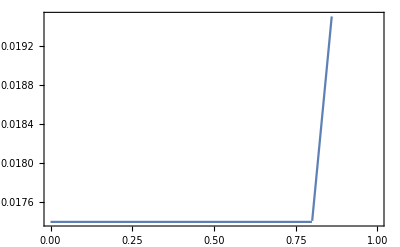

```mathematica
Plot[cd0[True,False,M],{M,0,1},Frame->True,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

Fighter aircraft C_D_0vs Mach

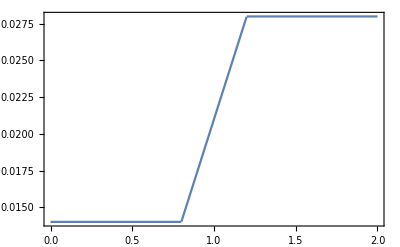

```mathematica
Plot[cd0[False,True,M],{M,0,2},Frame->True,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

### Propulsion: Thrust Lapse α

How (full) thrust varies with altitude and Mach number.

T=α T_SLS

### High bypass ratio Turbofan

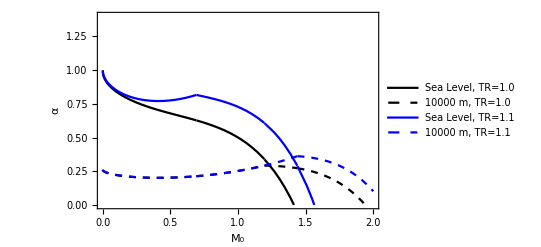

```mathematica
Plot[{αTF[0,M0,1.],αTF[10000,M0,1.],αTF[0,M0,1.1],αTF[10000,M0,1.1]},{M0,0,2},PlotRange->{All,{0,1.4}},FrameLabel->{"M_0","α"},PlotStyle->{{Black,Thick},{Black,Dashed},{Blue,Thick},{Blue,Dashed}},Frame->True,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],PlotLegends->{"Sea Level, TR=1.0","10000 m, TR=1.0","Sea Level, TR=1.1","10000 m, TR=1.1"}]
```

### Low bypass ratio Turbofan

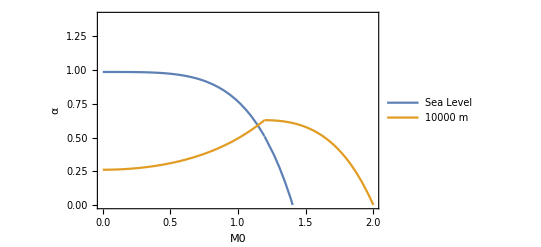

```mathematica
TR=1.0;
Plot[{αLTFmax[0,M0,TR],αLTFmax[10000,M0,TR]},{M0,0,2},PlotRange->{All,{0,1.4}},AxesLabel->{"M0","α"},PlotLegends->{"Sea Level","10000 m"},Frame->True,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

#### Military Power

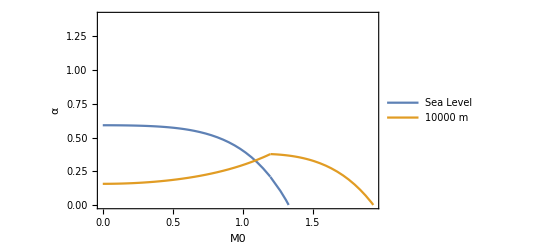

```mathematica
Plot[{αLTFmil[0,M0,TR],αLTFmil[10000,M0,TR]},{M0,0,2},PlotRange->{All,{0,1.4}},AxesLabel->{"M0","α"},PlotLegends->{"Sea Level","10000 m"},Frame->True,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

### Turbojet

#### Maximum Power

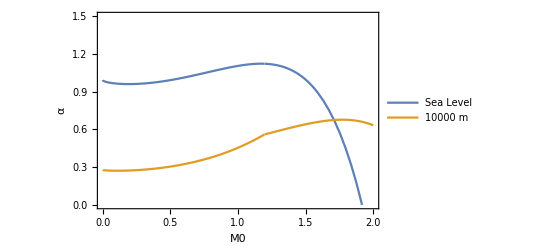

```mathematica
Plot[{αTJmax[0,M0,TR],αTJmax[10000,M0,TR]},{M0,0,2},PlotRange->{All,{0,1.5}},AxesLabel->{"M0","α"},PlotLegends->{"Sea Level","10000 m"},Frame->True,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

#### Military Power

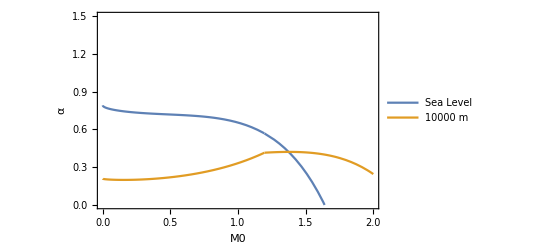

```mathematica
Plot[{αTJmil[0,M0,TR],αTJmil[10000,M0,TR]},{M0,0,2},PlotRange->{All,{0,1.5}},AxesLabel->{"M0","α"},PlotLegends->{"Sea Level","10000 m"},Frame->True,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

### Master Equation

```mathematica
RHS=β/α(q/(β WLG)(K1((n β)/q  WLG)^2+K2((n β)/q  WLG)+CD0+CDR)+Ps/V);
TW==RHS
```

TW==(β (Ps/V+(q (CD0+CDR+(K2 n WLG β)/q+(K1 n^2 WLG^2 β^2)/q^2))/(WLG β)))/α

### Flight Phases

#### Aircraft Settings

```mathematica
commercial=True;
If[commercial,fighter=False,fighter=True];

AR=8;
e=0.8;
TR=1.0;
```

#### Case 1: Constant Altitude/Speed Cruise (P_s=0)

dh/dt=0
dV/dt=0
n=1 (L=W)
q assigned

```mathematica
hcrz=11000;
p0crz=pstd[hcrz];
M0crz=0.85;
βcrz=0.85;

rule1={Ps->0,n->1,q->0.5 γ p0crz M0crz^2,M0->M0crz,h->hcrz,β->βcrz,α->αTF[hcrz,M0crz,TR],CDR->0,K1->k1[commercial,fighter,M0crz,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,M0crz],γ->1.4};
rule1//TableForm
```

Ps→0
n→1
q→8176.07 γ
M0→0.85
h→11000
β→0.85
α→0.196403
CDR→0
K1→0.0597359
K2→-0.004
CD0→0.01915
γ→1.4

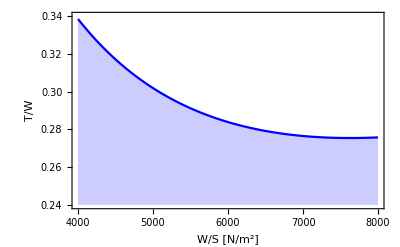

```mathematica
TW1=RHS//.rule1;
plot1=Plot[TW1,{WLG,4000,8000},Filling->Bottom,PlotRange->{All,{0.24,0.34}},Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

#### Case 2: Constant speed climb (P_s=dh/dt)

TO BE COMPLETED

dV/dt=0
n≈1
h assigned
dh/dt assigned
q assigned

#### Case 3: Constant speed/altitude turn (P_s=0)

dh/dt=0
dV/dt=0
n>1
h, q assigned

```mathematica
hTurn=11000;
p0Turn=pstd[hTurn];
βTurn=0.85;
nTurn=1.1;
M0Turn=0.85;

rule3={Ps->0,n->nTurn,q->0.5 γ p0Turn M0Turn^2,h->hTurn,β->βTurn,α->αTF[hTurn,M0Turn,TR],CDR->0,K1->k1[commercial,fighter,M0Turn,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,M0Turn],M0->M0Turn,γ->1.4};
rule3//TableForm
```

Ps→0
n→1.1
q→8176.07 γ
h→11000
β→0.85
α→0.196403
CDR→0
K1→0.0597359
K2→-0.004
CD0→0.01915
M0→0.85
γ→1.4

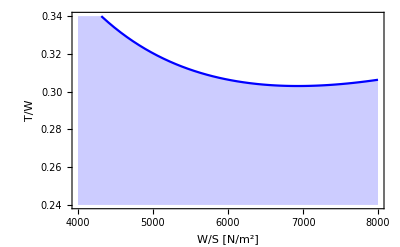

```mathematica
TW3 =RHS//.rule3;
plot3=Plot[TW3,{WLG,4000,8000},Filling->Bottom,PlotRange->{All,{0.24,0.34}},Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

#### Case 4: Horizontal acceleration

dh/dt=0
dV/dt assigned
n=1 (L=W)

```mathematica
g0=9.81;
hAcc=10000;
p0Acc=pstd[hAcc];
MAcc1=0.7;
MAcc2=0.8;
Mavg=(MAcc2+MAcc1)/2;
VAcc1=MAcc1*Sqrt[γ R Tstd[hAcc]];
VAcc2=MAcc2*Sqrt[γ R Tstd[hAcc]];
ΔT=180;
dV=(VAcc2-VAcc1)/ΔT;
βAcc=0.85;

rule4={Ps->V*dV/g0,n->1,q->0.5 γ p0Acc Mavg^2,h->hTurn,β->βAcc,α->αTF[hAcc,Mavg,TR],CDR->0,K1->k1[commercial,fighter,Mavg,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,Mavg],M0->Mavg,γ->1.4,R->287};
rule4//TableForm
```

Ps→0.000846167 V √(R γ)
n→1
q→7435.39 γ
h→11000
β→0.85
α→0.218123
CDR→0
K1→0.0597359
K2→-0.004
CD0→0.0174
M0→0.75
γ→1.4
R→287

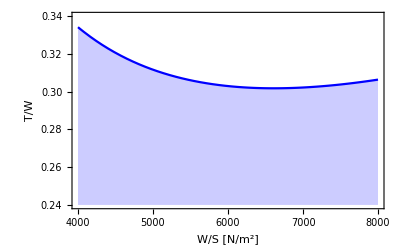

```mathematica
TW4 =RHS//.rule4;
plot4=Plot[TW4,{WLG,4000,8000},Filling->Bottom,Frame->True,PlotRange->{All,{0.24,0.34}},FrameLabel->{"W/S [N/m^2]","T/W"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

#### Case 5: Takeoff Roll (s_G) when T_SL>>(D+R)

dh/dt=0
s_G assigned
C_L_max assigned 
ρ assigned
V_TO=k_TOV_Stall

```mathematica
hfield=1500;
rule5={kTO->1.2,sG->2000,CLmax->2.4,β->1,α->αTF[hfield,0,TR],tr->0};
rule5//TableForm
```

kTO→1.2
sG→2000
CLmax→2.4
β→1
α→0.834505
tr→0

```mathematica
rule5colddensity=ρ->ρstd[hfield,-15.]
rule5hotdensity=ρ->ρstd[hfield,+30]
```

ρ→1.11852

ρ→0.955314

```mathematica
TW5=(β^2/α kTO^2/(sG ρ g0 CLmax)WLG);
```

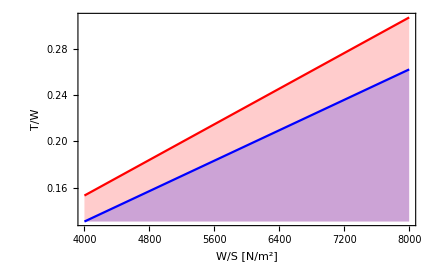

```mathematica
plot5=Plot[{TW5/.rule5hotdensity/.rule5,TW5/.rule5colddensity/.rule5},{WLG,4000,8000},Filling->Bottom,PlotStyle->{Red,Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

#### Case 8: Service Ceiling (P_s=dh/dt)

The maximum altitude at which the aircraft can cruise still having 100ft/min of remaining climb rate. The aircraft has to fly at its maximum efficiency attitude (C_L= √(C_D_0 π AR e)) and full thrust

dV/dt=0
n=1 
C_L assigned -> maximum efficiency C_L
h assigned
dh/dtassigned -> 0.5 m/s = 100 ft/min

```mathematica
ht=0.5;
hCeil=11500;
p0Ceil=pstd[hCeil];
βCeil=0.78;
M0Crit=0.8;
CLe=Sqrt[cd0[commercial,fighter,M0Crit]*Pi AR e];
```

```mathematica
rule8={Ps->ht,n->1,q->0.5 γ p0Ceil M0Crit^2,h->hCeil,β->βCeil,α->αTF[hCeil,M0Crit,TR],CDR->0,K1->k1[commercial,fighter,M0Crit,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,M0Ceil],V->Sqrt[2 β WLG /( ρstd[hCeil,0] CLe)],M0Ceil->V/Sqrt[γ R Tstd[hCeil]],γ->1.4,R->287.};
```

```mathematica
TW8 =RHS//.rule8;
```

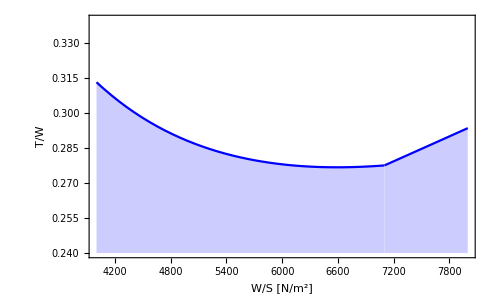

```mathematica
plot8=Plot[TW8,{WLG,4000,8000},Filling->Bottom,Frame->True,PlotRange->{All,{0.24,0.34}},FrameLabel->{"W/S [N/m^2]","T/W"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

### Constraint Diagram

The solution space is the white region over the constraint curves

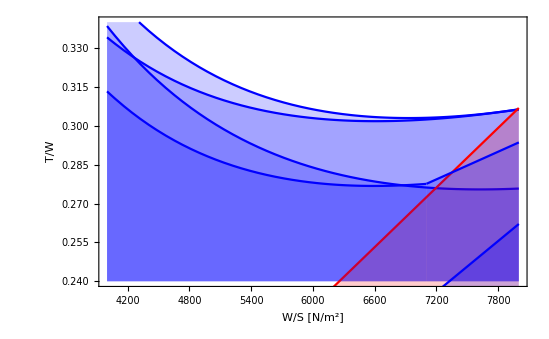

```mathematica
Show[plot1,plot3,plot4,plot5,plot8,Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

```mathematica
TWratio=0.31;
WLG0=6220.;
Print[Style["Aircraft characteristic ratios",20,Bold,Red]];
	Print[TableForm[
	{TWratio,WLG0},
	TableHeadings->{{"Take-Off-Thrust-to-MTOW ratio (T/W) ","Wing loading (W/S) "},None}
	]
];
```

Aircraft characteristic ratios

Take-Off-Thrust-to-MTOW ratio (T/W)  | 0.31
Wing loading (W/S)  | 6220.

### Constant PS contours

V(T-D)/W=(d(V^2/(2 g_0)+h))/dt=dz_e/dt=P_S

where z_e represents the aircraft mechanical energy (kinetic + potential) and is often referred to as “energy height”. P_S is the time rate of change of the energy height and is called weight specific excess power.

Once T/W and W/S are selected, it is possible to compute the weight specific excess power for flight at any chosen β, n, altitude, and velocity. Fighter pilots routinely compare these Ps diagrams for their aircraft with those of their potential adversaries in order to determine where in the flight envelope they enjoy the greatest combat advantage.

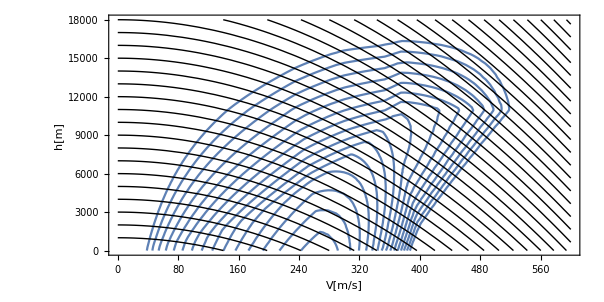

```mathematica
commercial=False;
fighter=True;

Quiet[rulePS={n->1,β->0.97,α->αTJmil[h,M0,1.0],TW->1.,WLG->4000,K1->k1[commercial,fighter,M0,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,M0],q->0.5 ρstd[h,0]V^2,M0->(V/Sqrt[γ R Tstd[h]]),AR->8,e->0.8,γ->1.4,R->287};]

Quiet[
Show[
Table[
ContourPlot[
Evaluate[V(α/β TW-K1 n^2 β/q WLG - K2 n - CD0/(β WLG/q))==cost//.rulePS],
{V,0,600},{h,0,18000},
AspectRatio->0.5,
ContourLabels->None,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],
Frame->True,
FrameLabel->{"V[m/s]","h[m]"}],
{cost,0,150,10}],
Table[ContourPlot[h+V^2/(2*9.81)==c1,{V,0,600},{h,0,18000},
ContourStyle->{Black,Thin},
ContourLabels->None],
{c1,0,38000,1000}]
]
]
```

## Mission Analysis

### TSFC Constants

```mathematica
c1TF=0.45;
c2TF=0.54;
c1LTFmil=0.9;
c2LTFmil=0.3;
c1LTFmax=1.6;
c2LTFmax=0.27;
c1TJmil=1.1;
c2TJmil=0.3;
c1TJmax=1.5;
c2TJmax=0.23;
```

### Best Subsonic Cruise (@ Best Mach = M_crit)

-Graphics-

```mathematica
piCRZ[ΔS_,C1_,C2_,M0_,CD0_,CDR_,K1_,K2_,a_]:=Exp[-(C1/M0+C2)/3600(√(4(CD0+CDR)K1)+K2)ΔS/a]
```

```mathematica
range=4100000; (*~ 2200 nm*)
AR=8;
e=0.8;
Mcrz=0.79;
commercial=True;
fighter=False;
```

```mathematica
ΠCRZ=piCRZ[ΔS,C1,C2,M0,CD0,CDR,K1,K2,a]//.{C1->0.45,C2->0.54,CD0->cd0[commercial,fighter,M0],CDR->0,K1->k1[commercial,fighter,M0,AR,e],K2->k2[commercial,fighter],M0->Mcrz,a->Sqrt[γ R Tstd[hcrz]],ΔS->range,γ->1.4,R->287.}
```

0.771843

### Best Subsonic Cruise Altitude

-Graphics-

#### Initial BCA

```mathematica
βinit=0.95;
WLG0=6220;
```

```mathematica
δinit=(2β)/(γ pstd[0] M0^2)1/(√((CD0+CDR)/K1))WLG0//.{CD0->cd0[commercial,fighter,M0],CDR->0,K1->k1[commercial,fighter,M0,AR,e],M0->0.8,β->βinit,γ->1.4}
```

0.241192

```mathematica
Quiet[BCAinit=h/.Solve[Reduce[δstd[h]==δinit],h][[1]]]
```

10509.5

```mathematica
Solve[delta==(2β)/(γa p0 M0^2)1/(√((CD0+CDR)/K1))WLG,β]
```

{{β→(delta √((CD0+CDR)/K1) M0^2 p0 γa)/(2 WLG)}}

#### 2000 ft steps

Step Climb

```mathematica
steps=Table[(delta √((CD0+CDR)/K1) M0^2 pstd[0] γ)/(2 WLG)//.{CD0->cd0[commercial,fighter,M0],CDR->0,K1->k1[commercial,fighter,M0,AR,e],WLG->WLG0,M0->0.8,delta->δstd[BCAinit+step/3.2808],γ->1.4},{step,2000,8000,2000}]
```

{0.863389,0.783287,0.709311,0.641097}

```mathematica
stepsrange=Quiet[Table[Solve[steps[[j]]==Exp[-(C1/M0+C2)/3600(√(4(CD0+CDR)K1)+K2)ΔS/a]//.{C1->0.45,C2->0.54,CD0->cd0[commercial,fighter,M0],CDR->0,K1->k1[commercial,fighter,M0,AR,e],K2->k2[commercial,fighter],M0->0.8,a->Sqrt[γ R Tstd[hcrz]],γ->1.4,R->287.},ΔS][[1,1]],{j,1,4}]]
```

{ΔS→2.34053×10^6,ΔS→3.89197×10^6,ΔS→5.47269×10^6,ΔS→7.08383×10^6}

```mathematica
ΔS1=ΔS/.stepsrange[[1]]
ΔS2=ΔS/.stepsrange[[2]]
ΔS3=ΔS/.stepsrange[[3]]
ΔS4=ΔS/.stepsrange[[4]]
```

2.34053×10^6

3.89197×10^6

5.47269×10^6

7.08383×10^6

### TO Weight estimation

```mathematica
Γ[WTO_]:=1.02*WTO^(-0.06);
seats=189+6;
baggage=90;
cargo = 3000;
Payload=80*seats+23*baggage+cargo;
Print["Payload = "<>ToString[Payload]]
```

Payload = 20670

```mathematica
WTOguess=200000.;
sol=FindRoot[WTOff==Payload/(1-βinit(1-ΠCRZ)-Γ[WTOff]),{WTOff,WTOguess}]
```

{WTOff→78168.5}

```mathematica
WTO=WTOff/.sol;
Wempty=Γ[WTO]*WTO;
Wfuel=WTO-Payload-Wempty;
Thrust=TWratio*WTO*9.81/2.; (*TWratio is a result of the constraint analysis; assuming twin-engine a/c*)
Print[Style["Aircraft Specifications",20,Bold,Red]];
	Print[TableForm[
	{WTO,Wempty,Payload,Wempty+Payload,Wfuel,Thrust},
	TableHeadings->{{"MTOW [Kg] ","OEW [Kg] ","Payload [Kg] ","MZFW [Kg]","MFW [Kg] ","TO Thrust (one engine) [N]"},None}
	]
];
```

Aircraft Specifications

MTOW [Kg]  | 78168.5
OEW [Kg]  | 40555.5
Payload [Kg]  | 20670
MZFW [Kg] | 61225.5
MFW [Kg]  | 16943.
TO Thrust (one engine) [N] | 118859.

### Payload-Range Diagram

This is a typical performance diagram of civil aviation aircrafts. It depicts the achievable mission range for a given payload.

```mathematica
Payload+(βinit*(1-ΠCRZ))*WTO+Wempty
```

78168.5

```mathematica
m2nm=0.000539957;(*meters to nautical miles*)
```

```mathematica
payloadrange={{0,Wempty+Payload},{range*m2nm,Wempty+Payload}};
towrange={{0,Wempty+Payload},{range*m2nm,Wempty+Payload+Wfuel}};
FuelCapacity = 20700;
PL=Payload;
Fu=Wfuel;
mtow=WTO;
newrange=range;
(*MTOW-limited range*)
While[Fu<FuelCapacity,
PL=PL-50;
Fu=WTO-Wempty-PL;
rangeguess=newrange;
sol=FindRoot[mtow==PL+βinit*(1-piCRZ[rng,c1TF,c2TF,Mcrz,cd0[commercial,fighter,Mcrz],0,k1[commercial,fighter,Mcrz,AR,e],k2[commercial,fighter],Sqrt[1.4*287* Tstd[hcrz]]])*mtow+Wempty,{rng,rangeguess}];
newrange=rng/.sol;
AppendTo[payloadrange,{newrange*m2nm,Wempty+PL}];
AppendTo[towrange,{newrange*m2nm,Wempty+PL+Fu}]
]
(*Fuel-capacity-limited range*)
While[PL>50,
PL=PL-50;
Fu=FuelCapacity;
tow=Wempty+Fu+PL;
rangeguess=newrange;
sol=FindRoot[tow==PL+βinit*(1-piCRZ[rng,c1TF,c2TF,Mcrz,cd0[commercial,fighter,Mcrz],0,k1[commercial,fighter,Mcrz,AR,e],k2[commercial,fighter],Sqrt[1.4*287* Tstd[hcrz]]])*tow+Wempty,{rng,rangeguess}];newrange=rng/.sol;
AppendTo[payloadrange,{newrange*m2nm,Wempty+PL}];
AppendTo[towrange,{newrange*m2nm,Wempty+PL+Fu}]
]
```

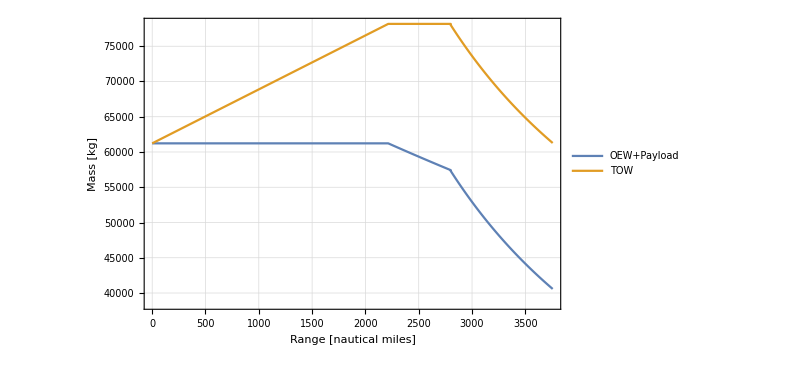

```mathematica
ListLinePlot[{payloadrange,towrange},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],
Frame->True,
FrameLabel->{"Range [nautical miles]","Mass [kg]"},
GridLines->Automatic,
PlotLegends->{"OEW+Payload","TOW"}]
```

## TurboJet Cycle Analysis

```mathematica
MOnD=.8;
z=10000.;
γair=1.4;
Rair=287;
ηd=.9;
ηf=.9;
ηmc=ηmf=.99;
ηc=.87;
BPR=5;
βf=1.5;
βc=15;
Qf=43500000.;
γgas=1.33;
Rgas=287;
ηb=.95;
ηpb=.95;
T4=1400.;
ηt=.98;
ηmt=.99;
ηn=.98;
{PointsTJ,energyTJ,performanceTJ}=CalcTurbojetCycle[MOnD,z,γair,Rair,ηd,ηmc,ηc,βc,Qf,γgas,Rgas,ηb,ηpb,T4,ηt,ηmt,ηn,True];
```

Engine Input Data

Engine Type: TurboJet

βc | 15
T4 | 1400.

Adiabatic efficiencies

ηd | 0.9
ηc | 0.87
ηb | 0.95
ηt | 0.98
ηn | 0.98

Mechanical & pneumatic efficiencies

ηmc | 0.99
ηmt | 0.99
ηpb | 0.95

Analysis Output

Free Stream Condition

Free Stream Static Condition

Height | 10. km
Mach | 0.8
Speed | 239.603 m/s
p_a | 26.4369 kPa
T_a | 223.252 K
ρ_a | 0.412604 kg/m^3
s_a | 0.182978 kJ/K

Free Stream Stagnation Condition

p_(0a) | 40.2989 kPa
T_(0a) | 251.828 K
ρ_(0a) | 0.557579 kg/m^3
s_(0a) | 0.182978 kJ/K

Ram diffusion

γ | 1.4
η_d | 0.9
p_02 | 38.7209 kPa
T_02 | 251.828 K
ρ_02 | 0.535746 kg/m^3
s_02 | 0.194441 kJ/K
Pressure ratio diffuser | 1.46465
Specific power | 0. kW/(kg/s)

Compressor compression

β_c | 15
γ | 1.4
η_c | 0.87
p_02 | 580.814 kPa
T_02 | 589.867 K
ρ_02 | 3.43084 kg/m^3
s_02 | 0.272211 kJ/K
Specific power | 339.56 kJ/kg

Burner

Burner Parameters

η_pb | 0.95
η_b | 0.95
p_02 | 551.773 kPa
T_02 | 1400. K
ρ_02 | 1.37325 kg/m^3
s_02 | 1.40387 kJ/K
f | 0.0258617
Specific power | 1068.73 kJ/kg

Turbine expansion

γ_gas | 1.33
η_t | 0.98
p_02 | 206.795 kPa
T_02 | 1103.47 K
ρ_02 | 0.652974 kg/m^3
s_02 | 1.41023 kJ/K
Turbine pressure ratio | 0.374783
Specific power | 342.99 kJ/kg

Nozzle expansion

Nozzle is choked

Nozzle Static Conditions

Pressure ratio nozzle | 1.87593
Speed | 601.291 m/s
Mach | 1.
p_e | 110.236 kPa
T_e | 947.189 K
ρ_e | 0.405513 kg/m^3
s_e | 1.41414 kJ/K

Nozzle Stagnation Conditions

p_02 | 198.963 kPa
T_02 | 1103.47 K
ρ_02 | 0.628244 kg/m^3
s_02 | 1.42131 kJ/K
Specific power | 0. kJ/kg

Engine Performance Parameters

Ia | 720.914 m/s
TSFC | 0.129144 N·kg/h
ηth | 0.153442
ηp | 0.272655
η0 | 0.562769

## TurboFan Cycle Analysis

```mathematica
MOnD=.8;
z=10000.;
γair=1.4;
Rair=287;
ηd=.9;
ηf=.9;
ηmc=ηmf=.99;
ηc=.87;
BPR=5;
βf=1.5;
βc=15;
Qf=43500000.;
γgas=1.33;
Rgas=287;
ηb=.95;
ηpb=.95;
T4=1400.;
ηt=.98;
ηmt=.99;
ηn=.98;
{corePointsTF,fanPointsTF,energyTF,performanceTF}=CalcTurboFanCycle[MOnD,z,γair,Rair,ηd,ηf,ηmf,BPR,βf,ηmc,ηc,βc,Qf,γgas,Rgas,ηb,ηpb,T4,ηt,ηmt,ηn,True];
```

Engine Input Data

Engine Type: TurboFan separate flows

βc | 15
βf | 1.5
BPR | 5
T4 | 1400.

Adiabatic efficiencies

ηd | 0.9
ηf | 0.9
ηc | 0.87
ηb | 0.95
ηt | 0.98
ηn | 0.98

Mechanical & pneumatic efficiencies

ηmf | 0.99
ηmc | 0.99
ηmt | 0.99
ηpb | 0.95

Analysis Output

Free Stream Condition

Free Stream Static Condition

Height | 10. km
Mach | 0.8
Speed | 239.603 m/s
p_a | 26.4369 kPa
T_a | 223.252 K
ρ_a | 0.412604 kg/m^3
s_a | 0.182978 kJ/K

Free Stream Stagnation Condition

p_(0a) | 40.2989 kPa
T_(0a) | 251.828 K
ρ_(0a) | 0.557579 kg/m^3
s_(0a) | 0.182978 kJ/K

Ram diffusion

γ | 1.4
η_d | 0.9
p_02 | 38.7209 kPa
T_02 | 251.828 K
ρ_02 | 0.535746 kg/m^3
s_02 | 0.194441 kJ/K
Pressure ratio diffuser | 1.46465
Specific power | 0. kW/(kg/s)

Fan compression

β_c | 1.5
γ | 1.4
η_c | 0.9
p_02 | 58.0814 kPa
T_02 | 286.196 K
ρ_02 | 0.707118 kg/m^3
s_02 | 0.206577 kJ/K
Specific power | 207.132 kJ/kg

Secondary nozzle expansion

Nozzle is adapted

Nozzle Static Conditions

Pressure ratio nozzle | 2.19698
Speed | 339.275 m/s
Mach | 1.12934
p_e | 26.4369 kPa
T_e | 236.439 K
ρ_e | 0.389593 kg/m^3
s_e | 0.218656 kJ/K

Nozzle Stagnation Conditions

p_02 | 55.3446 kPa
T_02 | 286.196 K
ρ_02 | 0.673799 kg/m^3
s_02 | 0.22753 kJ/K
Specific power | 0. kJ/kg

Compressor compression

β_c | 15
γ | 1.4
η_c | 0.87
p_02 | 871.221 kPa
T_02 | 670.367 K
ρ_02 | 4.52828 kg/m^3
s_02 | 0.284346 kJ/K
Specific power | 385.9 kJ/kg

Burner

Burner Parameters

η_pb | 0.95
η_b | 0.95
p_02 | 827.66 kPa
T_02 | 1400. K
ρ_02 | 2.05988 kg/m^3
s_02 | 1.2875 kJ/K
f | 0.0238251
Specific power | 984.574 kJ/kg

High pression turbine expansion

γ_gas | 1.33
η_t | 0.98
p_02 | 265.766 kPa
T_02 | 1063.01 K
ρ_02 | 0.871128 kg/m^3
s_02 | 1.29501 kJ/K
Turbine pressure ratio | 0.321106
Specific power | 389.798 kJ/kg

Low pression turbine expansion

γ_gas | 1.33
η_t | 0.98
p_02 | 123.221 kPa
T_02 | 882.127 K
ρ_02 | 0.486711 kg/m^3
s_02 | 1.29986 kJ/K
Turbine pressure ratio | 0.463643
Specific power | 209.224 kJ/kg

Primary nozzle expansion

Nozzle is choked

Nozzle Static Conditions

Pressure ratio nozzle | 1.87593
Speed | 537.612 m/s
Mach | 1.
p_e | 65.685 kPa
T_e | 757.19 K
ρ_e | 0.302259 kg/m^3
s_e | 1.30376 kJ/K

Nozzle Stagnation Conditions

p_02 | 118.554 kPa
T_02 | 882.127 K
ρ_02 | 0.468277 kg/m^3
s_02 | 1.31094 kJ/K
Specific power | 0. kJ/kg

Engine Performance Parameters

Ia | 175.118 m/s
TSFC | 0.0816312 N·kg/h
ηth | 0.242752
ηp | 0.310538
η0 | 0.781715

## Parametric Cycle Analysis

## Optimization

Finding the pareto front of the multi-objective problem (minimize TSFC and maximize Specific Thrust).

### Setting constant parameters

```mathematica
Ma=0.78;
h=10500.;
γair=1.4;
Rair=287.;
ηd=0.98;
ηmc=0.99;
ηc=0.9;
Qf=43500000.;
γgas=1.33;
Rgas=287;
ηb=.97;
ηpb=.98;
ηt=.95;
ηmt=.99;
ηn=.98;
report=True;
ηf=0.97;
ηmf=0.99;
```

### Exploring the design space and mapping it into the objectives space, then finding the pareto front

Number of succeded analyses: 40000 over 40000

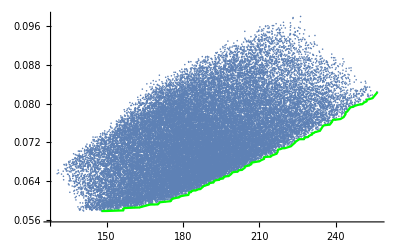

```mathematica
(*Definition of the ranges of the design variables (4D-space*)
βfRange={1.4,1.8};
βcRange={12.,15.};
T4Range={1200.,1600.};
BPRRange={4.,7.};

(*Number of samples to be mapped*)
Nsamples=40000;

(*Mapping of the designs into the output space*)
ProjVarsList={};
ObjVarsList={};
n=0;
For[i=1,i<Nsamples+1,i++,
βf=RandomReal[βfRange];
βc=RandomReal[βcRange];
T4=RandomReal[T4Range];
BPR=RandomReal[BPRRange];
ProjVars={βf,βc,T4,BPR};
AppendTo[ProjVarsList,ProjVars];
{corePoints,fanPoints,energy,performance}=CalcTurboFanCycle[Ma,h,γair,Rair,ηd,ηf,ηmf,BPR,βf,ηmc,ηc,βc,Qf,γgas,Rgas,ηb,ηpb,T4,ηt,ηmt,ηn,False];
{Ia,TSFC,ηo,ηth,ηp,specificThrust}=performance;
(*Checking if Cycle Analysis produced valid results. In that case, append results to ObjVarsList and update counter*)
If[NumericQ[Ia]==True,n++;ObjVars={Ia,TSFC,i};AppendTo[ObjVarsList,ObjVars]];
]
NsamplesNew=n;
Print["Number of succeded analyses: ", NsamplesNew, " over ", Nsamples];
allpts=ListPlot[Table[{ObjVarsList[[i,1]],ObjVarsList[[i,2]]},{i,1,NsamplesNew}]];

(*FInd the Pareto Front*)
IaSortedVars=Sort[ObjVarsList,#1[[1]]>#2[[1]]&];
BestTSFC=IaSortedVars[[1,2]];
paretoFront={IaSortedVars[[1]]};
Do[
If[IaSortedVars[[i+1,2]]<=BestTSFC,BestTSFC=IaSortedVars[[i+1,2]];AppendTo[paretoFront,IaSortedVars[[i+1]]]];
,{i,1,NsamplesNew-1}]
paretoplot=ListLinePlot[Table[{paretoFront[[i,1]],paretoFront[[i,2]]},{i,1,Dimensions[paretoFront][[1]]}],PlotStyle->Green];

(*Plot*)
Show[allpts,paretoplot]
```

### Finding chosen design based on a constraint on TSFC

```mathematica
targetTSFC=0.064;
Do[
If[paretoFront[[i,2]]<=targetTSFC,chosenPoint=paretoFront[[i,3]];Break[]]

,{i,1,Dimensions[paretoFront][[1]]}
];
Print["BEST sample #: ",chosenPoint]
```

BEST sample #: 38559

```mathematica
Do[
If[ObjVarsList[[i,3]]==chosenPoint,{IaDes,TSFCDes}={ObjVarsList[[i,1]],ObjVarsList[[i,2]]}],
{i,1,NsamplesNew}];
Print["OBJECTIVE Performance"];
Print["Design Ia  : ", IaDes];
Print["Design TSFC: ", TSFCDes];
{βfdes,βcdes,T4des,BPRdes}=ProjVarsList[[chosenPoint]];
Print["DESIGN Variables"];
Print["Design βf  : ", βfdes];
Print["Design βc  : ", βcdes];
Print["Design T4  : ", T4des];
Print["Design BPR : ", BPRdes];
{corePointsDes,fanPointsDes,energyDes,performanceDes}=CalcTurboFanCycle[Ma,h,γair,Rair,ηd,ηf,ηmf,BPRdes,βfdes,ηmc,ηc,βcdes,Qf,γgas,Rgas,ηb,ηpb,T4des,ηt,ηmt,ηn,False];
If[performanceDes[[1]]==IaDes && performanceDes[[2]]==TSFCDes,Print["Solution Verified!"]]
```

OBJECTIVE Performance

Design Ia  : 192.259

Design TSFC: 0.0639863

DESIGN Variables

Design βf  : 1.79467

Design βc  : 14.3992

Design T4  : 1456.15

Design BPR : 6.34081

Solution Verified!

```mathematica
desPointPlot=ListPlot[{{IaDes,TSFCDes}},PlotStyle->Red];
```

```mathematica
desPointLinePlot=ListPlot[{{-10,TSFCDes},{IaDes,TSFCDes}},Joined->True,PlotStyle->{Dashed,Red}];
```

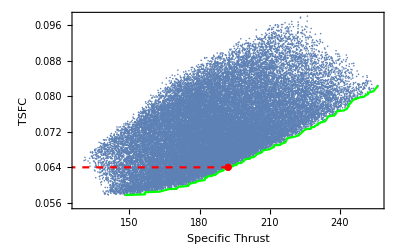

```mathematica
Show[allpts,paretoplot,desPointPlot,desPointLinePlot,Frame->True,FrameLabel->{"Specific Thrust","TSFC"},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

```mathematica
ThrustCRZ=αTF[10500.,0.78,1.]*Thrust;
mflowCRZ=ThrustCRZ/IaDes;
mflowcoreCRZ=mflowCRZ/(1+BPRdes);
Print[Style["Engine Design Choices and Performance",20,Bold,Red]];
	Print[TableForm[
	{BPRdes,βfdes,βcdes,T4des,ThrustCRZ,IaDes,TSFCDes,mflowCRZ,mflowcoreCRZ},
	TableHeadings->{{"BPR ","βf ","βc ","T4","CRZ Thrust (one engine) [N]","CRZ Specific Thrust [m/s]","CRZ TSFC [Kg/N hr]","CRZ air massflow [kg/s]","CRZ core air massflow [kg/s]"},None}
	]
];
```

Engine Design Choices and Performance

BPR  | 6.34081
βf  | 1.79467
βc  | 14.3992
T4 | 1456.15
CRZ Thrust (one engine) [N] | 24601.2
CRZ Specific Thrust [m/s] | 192.259
CRZ TSFC [Kg/N hr] | 0.0639863
CRZ air massflow [kg/s] | 127.959
CRZ core air massflow [kg/s] | 17.4312

## Compressor Sizing

## Mean Line Analysis

With given conditions, #Stages = 11 with ΔT0_stage = 36.6612

Compressor efficiency = 0.848646 with ΔT0_comp = 403.274

T0in = 293.052 :: T0out = 696.326

p0in = 65154.9 :: p0out = 977324.

Wheelspeed = 1942.75 rad/s

rmean = 0.115661

Stage # 1 Pratio = 1.44699 p0out = 94278.3 T0out = 329.714 Mout= 0.563409 α1 = 8.79503 β2 = 8.79503 , Δβ = 35.8796

Stage # 2 Pratio = 1.39135 p0out = 131174. T0out = 366.375 Mout= 0.532788 α1 = 8.79503 β2 = 8.79503 , Δβ = 35.8796

Stage # 3 Pratio = 1.34796 p0out = 176818. T0out = 403.036 Mout= 0.506672 α1 = 8.79503 β2 = 8.79503 , Δβ = 35.8796

Stage # 4 Pratio = 1.31319 p0out = 232197. T0out = 439.697 Mout= 0.484054 α1 = 8.79503 β2 = 8.79503 , Δβ = 35.8796

Stage # 5 Pratio = 1.28472 p0out = 298307. T0out = 476.359 Mout= 0.464218 α1 = 8.79503 β2 = 8.79503 , Δβ = 35.8796

Stage # 6 Pratio = 1.26097 p0out = 376156. T0out = 513.02 Mout= 0.446637 α1 = 8.79503 β2 = 8.79503 , Δβ = 35.8796

Stage # 7 Pratio = 1.24087 p0out = 466760. T0out = 549.681 Mout= 0.430913 α1 = 8.79503 β2 = 8.79503 , Δβ = 35.8796

Stage # 8 Pratio = 1.22363 p0out = 571143. T0out = 586.342 Mout= 0.41674 α1 = 8.79503 β2 = 8.79503 , Δβ = 35.8796

Stage # 9 Pratio = 1.20869 p0out = 690336. T0out = 623.004 Mout= 0.40388 α1 = 8.79503 β2 = 8.79503 , Δβ = 35.8796

Stage # 10 Pratio = 1.19562 p0out = 825381. T0out = 659.665 Mout= 0.392141 α1 = 8.79503 β2 = 8.79503 , Δβ = 35.8796

Stage # 11 Pratio = 1.18409 p0out = 977324. T0out = 696.326 Mout= 0.38137 α1 = 8.79503 β2 = 8.79503 , Δβ = 35.8796

Database contains: T,T0,p,p0,s,rmean,rtip,rhub,CrossSection,M,Mrel

Triangle contains: α1,α2,β1,β2,Ca,U,Cu1,Cu2,Wu1,Wu2,ω

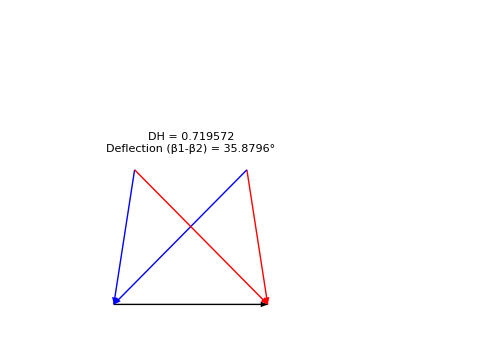

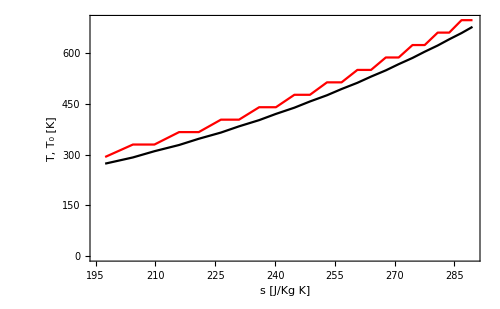

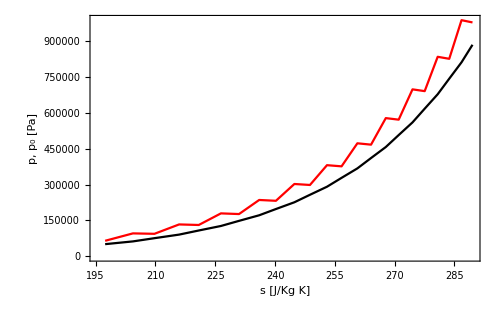

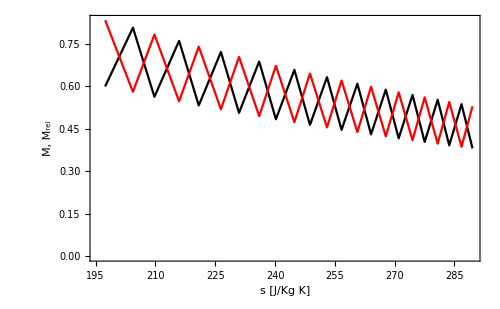

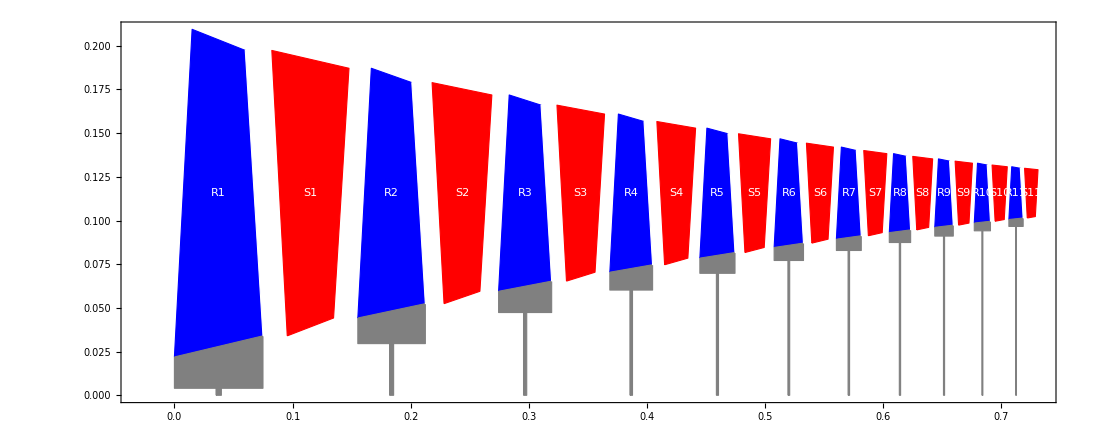

```mathematica
(*From cycle computations*)
T01=corePointsDes[[3,2]] ;                      (* [K]  *)
p01=corePointsDes[[3,1]]   ;      (*  [Pa] *)
βc=βcdes; 
γ=1.4;
Rair=287.;
cpAir=cp[γ,Rair];
massflow=mflowcoreCRZ ;      (*  [Kg/s] *) 
(*Aerodynamic design choices*)
Mach=0.6;
DF=0.55;
σ=1.1;
ΔT0stage=40.;
(*Structural design choices*)
σmaterial=344700000.;
ρblade=4680.;
taper=0.8;
(*Presumed stage efficiency, to be verified a-posteriori*)
etaStage=0.89;

{nStages,allStates,triangle,plot}=designMultiStageCompressor[T01,p01,βc,etaStage,γ,Rair,cpAir,Mach,DF,σ,ΔT0stage,massflow,σmaterial,ρblade,taper];
plot
nicePlotFromDB[allStates,5,1,2,"s [J/Kg K]","T, T_0 [K]"]
nicePlotFromDB[allStates,5,3,4,"s [J/Kg K]","p, p_0 [Pa]"]
nicePlotFromDB[allStates,5,10,11,"s [J/Kg K]","M, M_rel"]
drawCompressor[allStates,7,8,nStages]
```

#### Properties Across Stage along Mean Path Line

```mathematica
CompAreas=extractPropertyAlongCompressor[allStates,9,nStages]
```

{0.136238,0.103841,0.081629,0.0657646,0.0540549,0.0451751,0.0382874,0.0328414,0.0284638,0.0248942,0.0219468}

```mathematica
rMean=extractPropertyAlongCompressor[allStates,6,nStages]
```

{0.115661,0.115661,0.115661,0.115661,0.115661,0.115661,0.115661,0.115661,0.115661,0.115661,0.115661}

```mathematica
CompMeanDiameter=2*rMean
```

{0.231321,0.231321,0.231321,0.231321,0.231321,0.231321,0.231321,0.231321,0.231321,0.231321,0.231321}

```mathematica
rTip=extractPropertyAlongCompressor[allStates,7,nStages]
```

{0.209396,0.187106,0.171824,0.160908,0.152852,0.146742,0.142003,0.138256,0.135244,0.132789,0.130761}

```mathematica
rRoot=extractPropertyAlongCompressor[allStates,8,nStages]
```

{0.0219254,0.0442156,0.0594979,0.070413,0.0784696,0.0845791,0.089318,0.093065,0.0960769,0.0985328,0.100561}

```mathematica
α1m=Table[Deg2Rad[triangle[[1]]],{i,1,nStages}]
```

{0.153502,0.153502,0.153502,0.153502,0.153502,0.153502,0.153502,0.153502,0.153502,0.153502,0.153502}

```mathematica
β2m=Table[Deg2Rad[triangle[[4]]],{i,1,nStages}]
```

{0.153502,0.153502,0.153502,0.153502,0.153502,0.153502,0.153502,0.153502,0.153502,0.153502,0.153502}

```mathematica
phim=Table[triangle[[5]]/triangle[[6]],{i,1,nStages}]
```

{0.874564,0.874564,0.874564,0.874564,0.874564,0.874564,0.874564,0.874564,0.874564,0.874564,0.874564}

```mathematica
Ncomp=triangle[[6]]/(2 Pi rMean[[1]])
```

309.198

```mathematica
mredm=massflow*Sqrt[Rair allStates[[1,2]]]/(allStates[[1,4]] CompAreas[[1]])
```

0.5695

## Turbine Sizing

### Cycle Data

```mathematica
T0inlet=corePointsDes[[5,2]]
T0outlet=corePointsDes[[6,2]]
cpTurb=1234.;
```

1456.15

1129.78

### Design choice on rotational speed (to be checked with structural calculations, then iterated)

```mathematica
Uturb=360.;
```

## Automated Procedure

```mathematica
SizeTurbine[T0inlet,T0outlet,Uturb,cpTurb];
```

Number of stages = 2

Stage loadings =1.5538

stage #1

τ_stage | 0.887933
R | 0.231543
α2 | 54.3475
β2 | 26.1959
α3 | 0.436422
β3 | 42.2937
β2+β3 | 68.4896
Ca | 399.064

stage #2

τ_stage | 0.873788
R | 0.368846
α2 | 59.5555
β2 | 26.2467
α3 | 9.98812
β3 | 54.1594
β2+β3 | 80.4061
Ca | 316.168

## Diffuser Sizing

Subsonic Diffuser

## Cross-sections

### Tools

Diffuser law for isentropic flow:

A_0/A_1=M_1/M_0((1+(γ-1)/2 M_0^2)/(1+(γ-1)/2 M_1^2))^((γ+1)/(2(γ-1)))

### Data

Fan inlet:
- A_FAN=1.8112 m^2
- M_FAN=0.6
- r_tip= 0.771 m
- r_hub= 0.138 m

Refrence flight condition:
- M_0= 0.75

### Constraints

Lip Throat Mach number M_TH<0.75 to avoid sonic Mach numbers locally

⟹ M_TH= 0.7

N.B a thick Lip (large contraction ratio) helps at low speed and high AOA to prevent excessive flow distortion, but has bad high-speed performance (drag)

### Calculations

Station 1 = Throat
Station 2 = Spinner
Station 3 = Fan inlet

Hypothesis = external cowl has constant diameter over the spinner  
-Graphics-

Known/constrained quantities:

M_1=0.7
M_3=0.6
A_3=1.8112 m^2

Unknowns:

A_1
A_2
M_2

#### Cross-section at station 2

A_2=π r_tip^2

```mathematica
π 0.771^2
```

1.86749

#### Mach at station 2

```mathematica
rule={γ->1.4,Area2->1.86749,Area3->1.8112,Mach3->0.6};
dum=NSolve[Area2/Area3==Mach3/Mach2((1+(γ-1)/2 Mach2^2)/(1+(γ-1)/2 Mach3^2))^((γ+1)/(2(γ-1)))/.rule,Mach2]
```

{{Mach2→0.747472-3.72644 ⅈ},{Mach2→0.747472+3.72644 ⅈ},{Mach2→-1.81692-2.52306 ⅈ},{Mach2→-1.81692+2.52306 ⅈ},{Mach2→1.56802},{Mach2→0.57088}}

```mathematica
Mach2/.dum[[6]]
```

0.57088

#### Cross-section at station 1

```mathematica
rule2={γ->1.4,Area2->1.86749,Mach1->0.7,Mach2->0.57};
dum2=NSolve[Area1/Area2==Mach2/Mach1((1+(γ-1)/2 Mach1^2)/(1+(γ-1)/2 Mach2^2))^((γ+1)/(2(γ-1)))/.rule2,Area1]
```

{{Area1→1.66655}}

```mathematica
Area1/.dum2[[1]]
```

1.66655

## Capture Streamtube

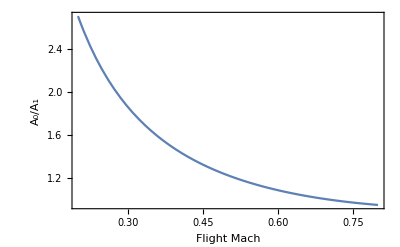

```mathematica
AreaRatio[M0_,M1_,γ_]:=M1/M0((1+(γ-1)/2 M0^2)/(1+(γ-1)/2 M1^2))^((γ+1)/(2(γ-1)));
Plot[AreaRatio[M0,0.7,1.4],{M0,0.2,0.8},Frame->True,FrameLabel->{"Flight Mach","A_0/A_1"}]
```

Supersonic Diffuser

#### Definitions

```mathematica
ARatioIsen[M_,gamma_]:=1/M(2/(gamma+1)(1+(gamma-1)/2 M^2))^((gamma+1)/(2(gamma-1)));
MafterNormalShock[M_,gamma_]:=√((2/(gamma-1)+M^2)/((2 gamma)/(gamma-1)M^2-1))/;M>1
MafterNormalShock[M_,gamma_]:=M/;M≤1

ARatioNonIsen[M_,gamma_]:=ARatioIsen[MafterNormalShock[M,gamma],gamma];
```

```mathematica
ARatioNonIsen[M,γ]//Simplify
```

(0.578704 (1+0.2 MafterNormalShock[M,1.4]^2)^3.)/MafterNormalShock[M,1.4]

#### Mach number downstream a normal shock

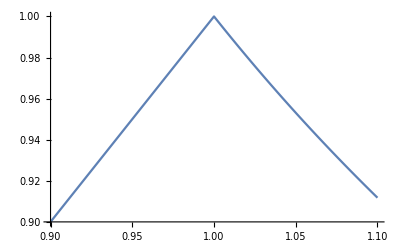

```mathematica
Plot[MafterNormalShock[M,1.4],{M,0.9,1.1}]
```

#### Area ratio in the isentropic case

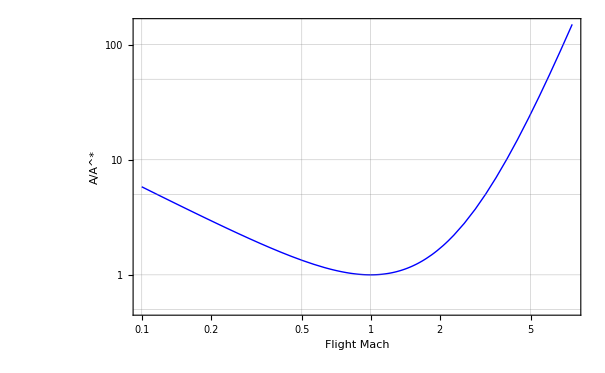

```mathematica
LogLogPlot[ARatioIsen[M,1.4],{M,0.1,20.},
Frame->True,
PlotStyle->{Blue,Thick},
PlotRange->{All,{0.5,150}},
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],
GridLines->Automatic,
FrameLabel->{"Flight Mach","A/A^*"}]
```

#### Area ratio in the non-isentropic case (with normal shock)

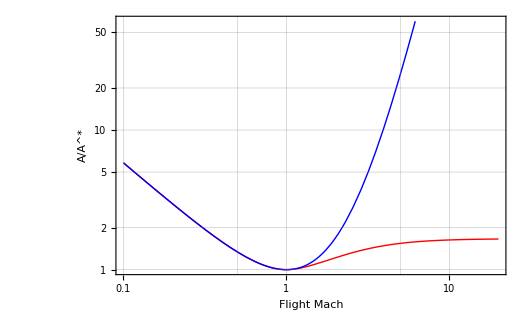

```mathematica
LogLogPlot[
{ARatioNonIsen[M,1.4],ARatioIsen[M,1.4]},{M,0.1,20.},
Frame->True,
PlotStyle->{{Red,Thick},{Blue,Thick}},
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],
GridLines->Automatic,
FrameLabel->{"Flight Mach","A/A^*"}]
```

#### Overspeeding

```mathematica
Manipulate[Module[{},
Mdes=M/.FindRoot[ARatioIsen[M,1.4]==aratgeo,{M,2}];
aratmod=ARatioNonIsen[Mdes,1.4];
Mos=M/.FindRoot[ARatioNonIsen[M,1.4]==aratgeo,{M,2}];
capture=ARatioNonIsen[M0,1.4]/aratgeo*100; (*assuming throat always chocked -> massflow requested downstream is the nominal one*)

Show[
LogLogPlot[aratgeo,{M,M1,M2},PlotStyle->Blue],
LogLogPlot[ARatioNonIsen[M,1.4],{M,M1,M2},PlotStyle->Darker[Red]],
LogLogPlot[ARatioIsen[M,1.4],{M,M1,M2},PlotStyle->Black],
Graphics[{PointSize[Large],Blue,Point[{Log[Mdes],Log[aratgeo]}]}],
Graphics[{PointSize[Large],Red,Point[{Log[Mdes],Log[aratmod]}]}],
Graphics[{PointSize[Large],Darker[Green],Point[{Log[Mos],Log[aratgeo]}]}],
Graphics[{PointSize[Large],Darker[Black],Point[{Log[M0],Log[ARatioNonIsen[M0,1.4]]}]}],
Frame->True,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],
FrameLabel->{"Flight Mach","Log A/A^*"},
AspectRatio->0.5,
PlotRange->{{Log[0.1],Log[10]},{Log[1],Log[3]}}
]
],

Panel[
Column[
{Style["Design Area Ratio",12],
Control[{{aratgeo,1.,""},1.,1.63,ControlType->Slider}],
Item[Text[Style["A/A^* = "Dynamic[aratgeo],14]],Alignment->Center],
Item[Text[Style["M_DESIGN = "Dynamic[Mdes],14,Blue]],Alignment->Center]}
]
],
Delimiter,
Item[Text[Style["Overspeeding",14]],Alignment->Center],
Item[Text[Style["M_OVERSPEED = "Dynamic[Mos],14,Darker[Green]]],Alignment->Center],
Panel[
Column[
{Style["Flight Mach Number",12],
Control[{{M0,0.1,""},0.01,Dynamic[Mos],ControlType->Slider}],
Item[Text[Style["M_FLIGHT = "Dynamic[M0],14]],Alignment->Center],
Item[Text[Style["% capture area = "Dynamic[capture],14,Blue]],Alignment->Center]}
]
],
ControlPlacement->Left,
TrackedSymbols:> {aratgeo,aratmod,Mdes,Mos,M0},
Initialization:>(ARatioIsen[M_,gamma_]:=1/M(2/(gamma+1)(1+(gamma-1)/2 M^2))^((gamma+1)/(2(gamma-1)));
MafterNormalShock[M_,gamma_]:=√((2/(gamma-1)+M^2)/((2 gamma)/(gamma-1)M^2-1))/;M>1;
MafterNormalShock[M_,gamma_]:=M/;M≤1;

ARatioNonIsen[M_,gamma_]:=ARatioIsen[MafterNormalShock[M,gamma],gamma];
M0=0.1;
M1=0.1;
M2=20;

)
]
```

## Compressor Performance Map

Off-Design behavior

### Off-design of multi-stage compressor at mean path line

Stage stacking: solve the stages sequentially 
The off-design outlet conditions of each stage are used as the inlet conditions of the following one.

Each stage produces a β_c which is function of m_red,N_red, ϕ_D, α_1, β_2  (the first 2 are off-design parameters, the last 3 are design parameters)

#### On-Design Check

Off-Design modules with design massflow and shaft speed should give the design β_c as solution

```mathematica
massflow
```

17.4312

```mathematica
Ncomp
```

309.198

```mathematica
{betaCmap,etaCmap,nredmap,delT0map,Machmap,lastStagemap,etaCmap1,perfoOnD,chokepoint}=multistageCompressorState[T01,p01,massflow,Ncomp,phim,Rair,γ ,α1m,β2m,CompAreas,CompMeanDiameter,etaStage];
TableForm[perfoOnD,TableHeadings->{None,{"betacn","delT0n","T0n","p0n","Can","Tn","Mn","phin","nredn","mredn"}}]
```

betacn | delT0n | T0n | p0n | Can | Tn | Mn | phin | nredn | mredn
1.44699 | 0.125101 | 329.714 | 94278.3 | 196.514 | 273.37 | 0.6 | 0.874564 | 0.246626 | 0.5695
1.39135 | 0.111191 | 366.375 | 131174. | 196.514 | 310.031 | 0.563409 | 0.874564 | 0.232511 | 0.547716
1.34796 | 0.100065 | 403.036 | 176818. | 196.514 | 346.692 | 0.532788 | 0.874564 | 0.220571 | 0.527882
1.31319 | 0.0909627 | 439.697 | 232197. | 196.514 | 383.353 | 0.506672 | 0.874564 | 0.2103 | 0.509824
1.28472 | 0.0833784 | 476.359 | 298307. | 196.514 | 420.015 | 0.484054 | 0.874564 | 0.201342 | 0.493348
1.26097 | 0.0769614 | 513.02 | 376156. | 196.514 | 456.676 | 0.464218 | 0.874564 | 0.193439 | 0.478269
1.24087 | 0.0714616 | 549.681 | 466760. | 196.514 | 493.337 | 0.446637 | 0.874564 | 0.1864 | 0.46442
1.22363 | 0.0666955 | 586.342 | 571143. | 196.514 | 529.998 | 0.430913 | 0.874564 | 0.180076 | 0.451656
1.20869 | 0.0625253 | 623.004 | 690336. | 196.514 | 566.66 | 0.41674 | 0.874564 | 0.174356 | 0.439851
1.19562 | 0.058846 | 659.665 | 825381. | 196.514 | 603.321 | 0.40388 | 0.874564 | 0.169148 | 0.428897
1.18409 | 0.0555756 | 696.326 | 977324. | 196.514 | 639.982 | 0.392141 | 0.874564 | 0.164381 | 0.4187

Overall compressor pressure ratio should be the design one:

```mathematica
βcdes
```

14.3992

```mathematica
betaCmap[[2]]
```

15.

All the intermediate flow conditions should be as per design.

#### Flow conditions along stages

Note that:
- Axial speed is constant (as per design)
- Speed of sound increases because temperature increases

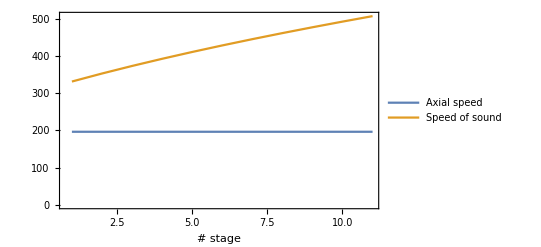

```mathematica
ListPlot[{Table[perfoOnD[[i,5]],{i,1,nStages}],Table[Sqrt[γ*Rgas*perfoOnD[[i,6]]],{i,1,nStages}]},Frame->True,Joined->True,PlotRange->{All,All},FrameLabel->{"# stage"},PlotLegends->{"Axial speed","Speed of sound"}]
```

Mach Number at stage outlet decreases as per design

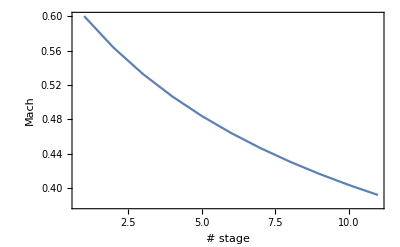

```mathematica
ListPlot[Table[perfoOnD[[i,7]],{i,1,nStages}],Frame->True,Joined->True,PlotRange->{All,All},FrameLabel->{"# stage","Mach"}]
```

#### Off-Design

Try to change either massflow or shaft speed (or both) and see what happens...

```mathematica
{betaCmap,etaCmap,nredmap,delT0map,Machmap,lastStagemap,etaCmap1,perfo,chokepoint}=multistageCompressorState[T01,p01,.6massflow, Ncomp,phim,Rair,γ ,α1m,β2m,CompAreas,CompMeanDiameter,etaStage];
TableForm[perfo,TableHeadings->{None,{"betacn","delT0n","T0n","p0n","Can","Tn","Mn","phin","nredn","mredn"}}]
```

betacn | delT0n | T0n | p0n | Can | Tn | Mn | phin | nredn | mredn
1.43565 | 0.146976 | 336.124 | 93539.9 | 103.906 | 287.55 | 0.309325 | 0.46242 | 0.246626 | 0.3417
1.38092 | 0.127161 | 378.866 | 129171. | 108.671 | 330.105 | 0.301938 | 0.483625 | 0.230283 | 0.334428
1.33833 | 0.112098 | 421.336 | 172873. | 112.593 | 372.404 | 0.294534 | 0.501082 | 0.216905 | 0.327078
1.30429 | 0.100257 | 463.578 | 225477. | 115.892 | 414.491 | 0.28736 | 0.515762 | 0.205683 | 0.319898
1.27646 | 0.0907002 | 505.624 | 287813. | 118.713 | 456.395 | 0.280519 | 0.52832 | 0.196088 | 0.312999
1.25331 | 0.0828226 | 547.501 | 360717. | 121.162 | 498.142 | 0.274044 | 0.539216 | 0.187758 | 0.306425
1.23373 | 0.076216 | 589.23 | 445029. | 123.311 | 539.752 | 0.267939 | 0.54878 | 0.180434 | 0.300185
1.21698 | 0.0705946 | 630.826 | 541591. | 125.216 | 581.239 | 0.262189 | 0.55726 | 0.173928 | 0.294274
1.20247 | 0.0657527 | 672.305 | 651247. | 126.92 | 622.616 | 0.256774 | 0.564841 | 0.168096 | 0.288675
1.18979 | 0.0615381 | 713.677 | 774848. | 128.454 | 663.895 | 0.251669 | 0.57167 | 0.162828 | 0.283372
1.17861 | 0.0578357 | 754.953 | 913245. | 129.845 | 705.084 | 0.246852 | 0.57786 | 0.158038 | 0.278344

Note that:

- axial speed is not constant anymore. It decreases/increases with higher/lower-than-design shaft speed to compensate for higher/lower density. In fact, a different shaft speed causes lower/higher pressure/density rise along stages, and given that the cross-section profile is fixed, the axial speed variation is the only way to maintain a constant massflow.

Usually (but not as a general rule):
- Mach number increases when wheel-speed is lower-than-design, at least in the rear stages (risk of rear-stages choking)

This happens because lower wheel speed means less energy is transferred to the flow along the compressor, so its axial velocity will increase going forward (to compensate for lower density) and the static temperature will be lower as well (and the speed of sound, in turn). The result is that Mach=1 can be reached at some point. The lower the wheel speed, the lower the massflow that causes rear stages choking.

- Mach number decreases when wheel-speed is higher-than-design (only the first stage can choke, if massflow is increased). 

Actually, is the ratio of massflow to wheel speed that governs the rear stages choking....

```mathematica
SetDirectory[NotebookDirectory[]]

<< ModulesForAircraftEngine`
```

/Volumes/GoogleDrive/Shared drives/DIDATTICA/MA/materiale didattico/Esercitazioni/current/AircraftEngineFramework_2.0

#### Case 1 : lower-than design shaft-speed ⟹ Risk of rear stages choking

```mathematica
{betaCmap,etaCmap,nredmap,delT0map,Machmap,lastStagemap,etaCmap1,perfo,chokepoint}=multistageCompressorState[T01,p01,massflow,.95Ncomp,phim,Rair,γ ,α1m,β2m,CompAreas,CompMeanDiameter,etaStage];
TableForm[perfo,TableHeadings->{None,{"betacn","delT0n","T0n","p0n","Can","Tn","Mn","phin","nredn","mredn"}}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

betacn | delT0n | T0n | p0n | Can | Tn | Mn | phin | nredn | mredn
1.38266 | 0.110699 | 325.493 | 90087. | 196.514 | 273.37 | 0.6 | 0.920594 | 0.234295 | 0.5695
1.3261 | 0.0975244 | 357.237 | 119464. | 207.116 | 303.629 | 0.600031 | 0.970259 | 0.222313 | 0.569518
1.28067 | 0.0867302 | 388.22 | 152995. | 218.678 | 332.864 | 0.605068 | 1.02442 | 0.212206 | 0.572352
1.24267 | 0.0775961 | 418.344 | 190122. | 231.739 | 360.849 | 0.61584 | 1.08561 | 0.203562 | 0.57828
1.20952 | 0.0696043 | 447.463 | 229957. | 247.034 | 387.241 | 0.633722 | 1.15726 | 0.196096 | 0.587716
1.17921 | 0.0623245 | 475.351 | 271166. | 265.749 | 411.468 | 0.661356 | 1.24493 | 0.189608 | 0.601313
1.14958 | 0.0552884 | 501.632 | 311727. | 290.18 | 432.434 | 0.704433 | 1.35938 | 0.183962 | 0.620131
1.11688 | 0.0476351 | 525.527 | 348162. | 326.466 | 447.311 | 0.779228 | 1.52936 | 0.179078 | 0.646048

Axial speed VS speed of sound

```mathematica
nstgs=Dimensions[perfo][[1]];
```

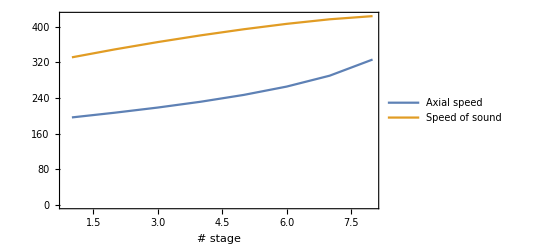

```mathematica
ListPlot[{Table[perfo[[i,5]],{i,1,nstgs}],Table[Sqrt[γ*Rgas*perfo[[i,6]]],{i,1,nstgs}]},Frame->True,Joined->True,PlotRange->{All,All},FrameLabel->{"# stage"},PlotLegends->{"Axial speed","Speed of sound"}]
```

Mach Number increases!

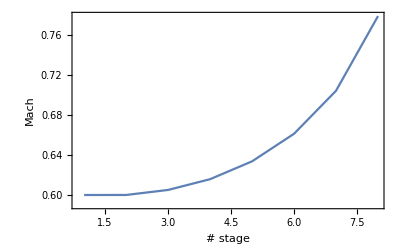

```mathematica
ListPlot[Table[perfo[[i,7]],{i,1,nstgs}],Frame->True,Joined->True,PlotRange->{All,All},FrameLabel->{"# stage","Mach"}]
```

#### Case 1b : higher-than design massflow ⟹ Risk of rear stages choking

```mathematica
{betaCmap,etaCmap,nredmap,delT0map,Machmap,lastStagemap,etaCmap1,perfo,chokepoint}=multistageCompressorState[T01,p01,1.1massflow,Ncomp,phim,Rair,γ ,α1m,β2m,CompAreas,CompMeanDiameter,etaStage];
TableForm[perfo,TableHeadings->{None,{"betacn","delT0n","T0n","p0n","Can","Tn","Mn","phin","nredn","mredn"}}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

betacn | delT0n | T0n | p0n | Can | Tn | Mn | phin | nredn | mredn
1.38738 | 0.116582 | 327.217 | 90394.5 | 232.583 | 265.482 | 0.720596 | 1.03508 | 0.246626 | 0.62645
1.32501 | 0.1017 | 360.495 | 119774. | 245.392 | 296.526 | 0.719384 | 1.09209 | 0.233396 | 0.62599
1.2727 | 0.0891646 | 392.638 | 152437. | 261.783 | 325.567 | 0.732409 | 1.16504 | 0.222363 | 0.630817
1.22506 | 0.0778734 | 423.214 | 186745. | 284.426 | 351.407 | 0.765942 | 1.2658 | 0.213067 | 0.642059
1.17376 | 0.0660863 | 451.183 | 219194. | 322.095 | 370.338 | 0.844921 | 1.43344 | 0.205226 | 0.661999

Axial speed VS speed of sound

```mathematica
nstgs=Dimensions[perfo][[1]];
```

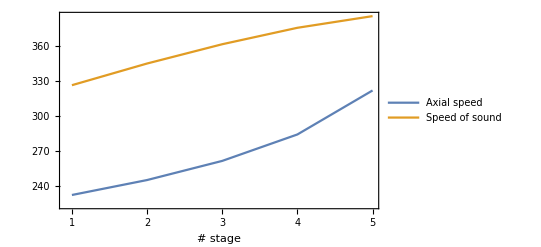

```mathematica
ListPlot[{Table[perfo[[i,5]],{i,1,nstgs}],Table[Sqrt[γ*Rgas*perfo[[i,6]]],{i,1,nstgs}]},Frame->True,Joined->True,PlotRange->{All,All},FrameLabel->{"# stage"},PlotLegends->{"Axial speed","Speed of sound"}]
```

Mach Number increases!

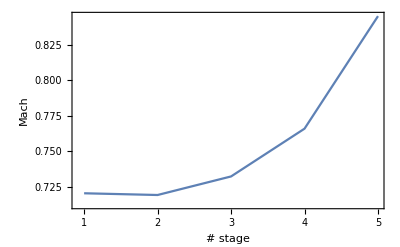

```mathematica
ListPlot[Table[perfo[[i,7]],{i,1,nstgs}],Frame->True,Joined->True,PlotRange->{All,All},FrameLabel->{"# stage","Mach"}]
```

#### Case 2 : higher-than design shaft-speed

```mathematica
{betaCmap,etaCmap,nredmap,delT0map,Machmap,lastStagemap,etaCmap1,perfo,chokepoint}=multistageCompressorState[T01,p01,massflow,1.2Ncomp,phim,Rair,γ ,α1m,β2m,CompAreas,CompMeanDiameter,etaStage];
TableForm[perfo,TableHeadings->{None,{"betacn","delT0n","T0n","p0n","Can","Tn","Mn","phin","nredn","mredn"}}]
```

betacn | delT0n | T0n | p0n | Can | Tn | Mn | phin | nredn | mredn
1.73942 | 0.191286 | 349.109 | 113332. | 196.514 | 273.37 | 0.6 | 0.728804 | 0.295952 | 0.5695
1.59629 | 0.168296 | 407.863 | 180910. | 164.047 | 335.393 | 0.452192 | 0.608393 | 0.271152 | 0.468845
1.48493 | 0.147297 | 467.94 | 268638. | 148.114 | 396.682 | 0.37541 | 0.549302 | 0.250863 | 0.403847
1.40679 | 0.129856 | 528.705 | 377916. | 139.834 | 457.974 | 0.329855 | 0.518594 | 0.234206 | 0.361578
1.35057 | 0.115632 | 589.84 | 510404. | 135.377 | 519.364 | 0.299875 | 0.502065 | 0.220337 | 0.332386
1.30852 | 0.103982 | 651.173 | 667873. | 133. | 580.824 | 0.278588 | 0.493252 | 0.208606 | 0.311043
1.27591 | 0.0943366 | 712.602 | 852148. | 131.834 | 642.314 | 0.262594 | 0.488925 | 0.198539 | 0.29469
1.24988 | 0.0862544 | 774.067 | 1.06508×10^6 | 131.405 | 703.801 | 0.250045 | 0.487334 | 0.189788 | 0.281679
1.22859 | 0.0794014 | 835.529 | 1.30855×10^6 | 131.441 | 765.261 | 0.239861 | 0.48747 | 0.182098 | 0.271007
1.21083 | 0.0735272 | 896.963 | 1.58444×10^6 | 131.778 | 826.678 | 0.231369 | 0.488717 | 0.175272 | 0.262034
1.19578 | 0.068442 | 958.353 | 1.89464×10^6 | 132.309 | 888.041 | 0.224133 | 0.490688 | 0.169163 | 0.254336

Axial speed VS speed of sound

```mathematica
nstgs=Dimensions[perfo][[1]];
```

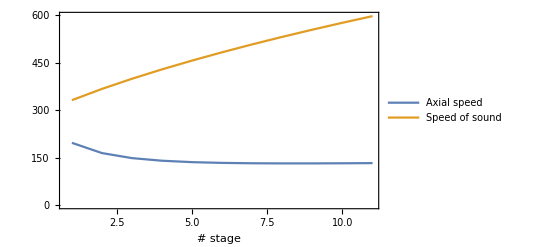

```mathematica
ListPlot[{Table[perfo[[i,5]],{i,1,nstgs}],Table[Sqrt[γ*Rgas*perfo[[i,6]]],{i,1,nstgs}]},Frame->True,Joined->True,PlotRange->{All,All},FrameLabel->{"# stage"},PlotLegends->{"Axial speed","Speed of sound"}]
```

Mach Number decreases

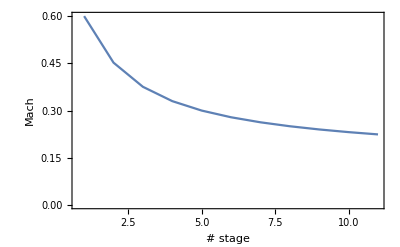

```mathematica
ListPlot[Table[perfo[[i,7]],{i,1,nstgs}],Frame->True,Joined->True,PlotRange->{All,All},FrameLabel->{"# stage","Mach"}]
```

#### Case 3 : higher-than design massflow and shaft speed ⟹ Risk of first stage choking

```mathematica
{betaCmap,etaCmap,nredmap,delT0map,Machmap,lastStagemap,etaCmap1,perfo,chokepoint}=multistageCompressorState[T01,p01,1.1massflow,1.05Ncomp,phim,Rair,γ ,α1m,β2m,CompAreas,CompMeanDiameter,etaStage];
TableForm[perfo,TableHeadings->{None,{"betacn","delT0n","T0n","p0n","Can","Tn","Mn","phin","nredn","mredn"}}]
```

betacn | delT0n | T0n | p0n | Can | Tn | Mn | phin | nredn | mredn
1.45246 | 0.131416 | 331.564 | 94635.1 | 232.583 | 265.482 | 0.720596 | 0.985791 | 0.258958 | 0.62645
1.39877 | 0.116903 | 370.325 | 132373. | 229.155 | 304.8 | 0.662603 | 0.971263 | 0.243454 | 0.601898
1.35603 | 0.105193 | 409.28 | 179502. | 226.477 | 344.183 | 0.616257 | 0.959914 | 0.230361 | 0.578505
1.32134 | 0.0955699 | 448.395 | 237184. | 224.284 | 383.642 | 0.578051 | 0.950616 | 0.219124 | 0.556685
1.29271 | 0.0875346 | 487.645 | 306609. | 222.423 | 423.181 | 0.54582 | 0.942732 | 0.209349 | 0.536501
1.2687 | 0.0807304 | 527.013 | 388995. | 220.803 | 462.797 | 0.518135 | 0.935866 | 0.200747 | 0.517879
1.24831 | 0.0748985 | 566.486 | 485585. | 219.363 | 502.488 | 0.494006 | 0.92976 | 0.193104 | 0.500693
1.23078 | 0.0698468 | 606.053 | 597647. | 218.06 | 542.251 | 0.472724 | 0.924238 | 0.186255 | 0.484806
1.21556 | 0.0654301 | 645.707 | 726476. | 216.865 | 582.083 | 0.453762 | 0.919171 | 0.180072 | 0.470087
1.20223 | 0.0615368 | 685.442 | 873392. | 215.755 | 621.981 | 0.436722 | 0.91447 | 0.174455 | 0.456413
1.19046 | 0.0580797 | 725.252 | 1.03974×10^6 | 214.716 | 661.944 | 0.421294 | 0.910064 | 0.169323 | 0.443675

Axial speed VS speed of sound

```mathematica
nstgs=Dimensions[perfo][[1]];
```

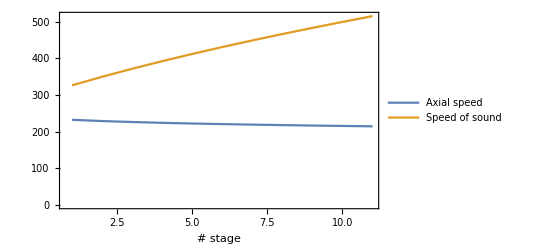

```mathematica
ListPlot[{Table[perfo[[i,5]],{i,1,nstgs}],Table[Sqrt[γ*Rgas*perfo[[i,6]]],{i,1,nstgs}]},Frame->True,Joined->True,PlotRange->{All,All},FrameLabel->{"# stage"},PlotLegends->{"Axial speed","Speed of sound"}]
```

Mach Number decreases, but is near 1 at inlet!

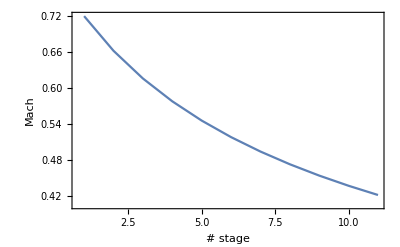

```mathematica
ListPlot[Table[perfo[[i,7]],{i,1,nstgs}],Frame->True,Joined->True,PlotRange->{All,All},FrameLabel->{"# stage","Mach"}]
```

Generate Map

#### Compressor Map

The map is built evaluating the pressure ratio at various combinations of massflows and wheel speed. 

First, the maximum massflow is calculated as the massflow at which the first stage chokes (i.e. Mach=1 at compressor inlet). It does not depend upon the wheel speed (if large enough). This massflow defines the right-hand limit of the compressor map. No massflows higher than this can be elaborated by the compressor. 

Then, for each combination of massflow and wheel speed, the pressure ratio is calculated via a stage stacking method (going sequentially through all the stages). 

The shape of the constant wheel curves will resemble the single-stage psi-phi curves. 

Note that for some combinations (generally at low wheel speed), rear stages choking will occur. The “chocked” states are cut out of the map. 

Compressor stability boundary is the maximum of the curves

First stage choking occurs at massflow = 21.4312

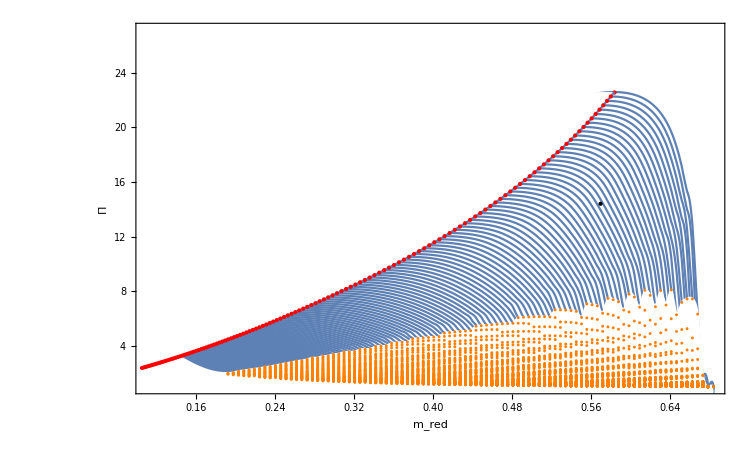

```mathematica
(*Generating Compressor Map*)
mapResolution=128; (*High resolution is required for the interpolation accuracy. Minimum 128, suggested 256*)
nrng=mapResolution;nmflow=mapResolution;
dump=True;
T02OnD=corePointsDes[[3,2]] ;  
p02OnD=corePointsDes[[3,1]] ; 
mapPlot=Quiet[multistageCompressorMap[massflow, Ncomp, nrng,nmflow,T02OnD,p02OnD, phim,Rair,γair,α1m,β2m,CompAreas,CompMeanDiameter,etaStage,mapResolution,dump]];

(*Get Design Point*)
pointOnD=plotPoint[mredm,βcdes,Black];

Show[mapPlot,pointOnD]
```

Play with Off-Design

```mathematica
Manipulate[{betaCmap,etaCmap,nredmap,delT0map,Machmap,lastStagemap,etaCmap1,perfo,chokepoint}=Quiet[multistageCompressorState[T01,p01,dm*massflow, dn*Ncomp,phim,Rair,γ ,α1m,β2m,CompAreas,CompMeanDiameter,etaStage]];
plotPhi=Show[ListPlot[Table[perfoOnD[[i,8]],{i,1,nStages}],Joined->True,PlotStyle->Black,Frame->True,Axes->False,FrameLabel->{"n Stage"},PlotLabel->Style["ϕ",18]],ListPlot[Table[perfo[[i,8]],{i,1,Length[perfo]}],Joined->True,PlotStyle->Red,Frame->True,Axes->False],ImageSize->400];
plotCa=Show[ListPlot[Table[perfoOnD[[i,5]],{i,1,nStages}],Joined->True,PlotStyle->Black,Frame->True,Axes->False,FrameLabel->{"n Stage"},PlotLabel->Style["Axial Speed",18]],ListPlot[Table[perfo[[i,5]],{i,1,Length[perfo]}],Joined->True,PlotStyle->Red,Frame->True,Axes->False],ImageSize->400,PlotRange->{{1,nStages},{50,500}}];
plotRho0=Show[ListPlot[Table[(perfoOnD[[i,4]]/(Rgas*perfoOnD[[i,3]])),{i,1,nStages}],Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"n Stage"},PlotLabel->Style["Total density",18]],ListPlot[Table[(perfo[[i,4]]/(Rgas*perfo[[i,3]])),{i,1,Length[perfo]}],Joined->True,PlotStyle->Red,Frame->True],ImageSize->400];
plotMach=Show[ListPlot[Table[perfoOnD[[i,7]],{i,1,nStages}],Joined->True,PlotStyle->Black,Frame->True,Axes->False,FrameLabel->{"n Stage"},PlotLabel->Style["Axial Mach",18]],ListPlot[Table[perfo[[i,7]],{i,1,Length[perfo]}],Joined->True,PlotStyle->Red,Frame->True,Axes->False],ImageSize->400,PlotRange->{{1,nStages},{0.2,1}}];
plotSpdSnd=Show[ListPlot[Table[Sqrt[γ*Rgas*perfoOnD[[i,6]]],{i,1,nStages}],Joined->True,PlotStyle->Black,Frame->True,Axes->False,FrameLabel->{"n Stage"},PlotLabel->Style["Speed of Sound",18]],ListPlot[Table[Sqrt[γ*Rgas*perfo[[i,6]]],{i,1,Length[perfo]}],Joined->True,PlotStyle->Red,Frame->True,Axes->False],ImageSize->400,PlotRange->{{1,nStages},{50,500}}];
plotBetaC=Show[ListPlot[Table[perfoOnD[[i,1]],{i,1,nStages}],Joined->True,PlotStyle->Black,Frame->True,Axes->False,FrameLabel->{"n Stage"},PlotLabel->Style["βc",18]],ListPlot[Table[perfo[[i,1]],{i,1,Length[perfo]}],Joined->True,PlotStyle->Red,Frame->True,Axes->False],ImageSize->400];
map=Show[mapPlot,pointOnD,plotPoint[betaCmap[[1,1]],betaCmap[[2]],Red],ImageSize->600];
Grid[{{plotCa,plotSpdSnd,plotMach},{plotPhi,plotRho0,plotBetaC},{map,SpanFromLeft}}]
,{{dm,1.},0.2,1.1},{{dn,1.},0.2,1.1}]
```

Table::iterb: Iterator {i,1,nStages} does not have appropriate bounds.

Table::iterb: Iterator {i,1.,nStages} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListPlot::lpn: Table[perfoOnD⟦i,8⟧,{i,1.,nStages}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStages} does not have appropriate bounds.

Table::iterb: Iterator {i,1.,nStages} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListPlot::lpn: Table[perfoOnD⟦i,8⟧,{i,1.,nStages}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStages} does not have appropriate bounds.

Table::iterb: Iterator {i,1.,nStages} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListPlot::lpn: Table[perfoOnD⟦i,8⟧,{i,1.,nStages}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStages} does not have appropriate bounds.

Table::iterb: Iterator {i,1.,nStages} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListPlot::lpn: Table[perfoOnD⟦i,8⟧,{i,1.,nStages}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Table::iterb: Iterator {i,1,nStages} does not have appropriate bounds.

Table::iterb: Iterator {i,1.,nStages} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::nliter: Non-list iterator VectorQ[{i,1,nStages}] at position 2 does not evaluate to a real numeric value.

ListPlot::lpn: Table[perfoOnD⟦i,8⟧,{i,1.,nStages}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Table[perfoOnD⟦i,8⟧,{i,1,nStages}],Joined→True,PlotStyle→color,Frame→True,Axes→False,FrameLabel→{n Stage},PlotLabel→ϕ],,ImageSize→400].

Table::nliter: Non-list iterator VectorQ[{i,1,nStages}] at position 2 does not evaluate to a real numeric value.

ListPlot::lpn: Table[perfoOnD⟦i,5⟧,{i,1.,nStages}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Table[perfoOnD⟦i,5⟧,{i,1,nStages}],Joined→True,PlotStyle→color,Frame→True,Axes→False,FrameLabel→{n Stage},PlotLabel→Axial Speed],,ImageSize→400,PlotRange→{{1,nStages},{50,500}}].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Table::nliter: Non-list iterator VectorQ[{i,1,nStages}] at position 2 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

ListPlot::lpn: Table[perfoOnD⟦i,4⟧/(Rgas perfoOnD⟦i,3⟧),{i,1.,nStages}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

## Full Design + Off-Design Component Matching (TurboJet)

## Rolls-Royce / SNECMA Olympus 593

```mathematica
-Graphics--Graphics-
```

Thrust @ SL = 31,350 lbf = 139,8 kN
Airflow @ SL = 410 lb/s = 186 kg/s
FC @ SL = 1.39 lb/lbf/hr = 19800 kg/hr

Free Memory

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]

<< ModulesForAircraftEngine`
```

/Users/riccardo/Library/CloudStorage/GoogleDrive-riccardo.malpicagalassi@uniroma1.it/My Drive/AircraftEngineFramework-dev

```mathematica
MOnD=.4;
z=1000.;
γair=1.4;
Rair=287;
ηd=.9;
ηmc=.99;
ηc=.87;
βc=15;
Qf=43500000.;
γgas=1.33;
Rgas=287;
ηb=.95;
ηpb=.95;
T4=1400.;
ηt=.98;
ηmt=.99;
ηn=.98;
massflowOnD=180;

(*Aerodynamic design choices*)
Mach=0.6;
DF=0.55;
σ=1.1;
ΔT0stage=35.;
(*Structural design choices*)
σmaterial=344700000.;
ρblade=4680.;
taper=0.8;
(*Presumed stage efficiency, to be verified a-posteriori*)
etaStage=0.89;
compressorDesignChoices={Mach,ΔT0stage,etaStage,DF,σ,σmaterial,ρblade,taper};

enginePars={MOnD,z,γair,Rair,ηd,ηmc,ηc,βc,Qf,γgas,Rgas,ηb,ηpb,T4,ηt,ηmt,ηn,massflowOnD,compressorDesignChoices};
compressorMapResolution=32;

{designPars,varsOnD,compressorMap}=BuildEngine[enginePars,compressorMapResolution,True];
```

Engine Input Data

Engine Type: TurboJet

βc | 15
T4 | 1400.

Adiabatic efficiencies

ηd | 0.9
ηc | 0.87
ηb | 0.95
ηt | 0.98
ηn | 0.98

Mechanical & pneumatic efficiencies

ηmc | 0.99
ηmt | 0.99
ηpb | 0.95

Analysis Output

Free Stream Condition

Free Stream Static Condition

Height | 1. km
Mach | 0.4
Speed | 134.561 m/s
p_a | 89.8748 kPa
T_a | 281.651 K
ρ_a | 1.11185 kg/m^3
s_a | 0.0652015 kJ/K

Free Stream Stagnation Condition

p_(0a) | 100.35 kPa
T_(0a) | 290.664 K
ρ_(0a) | 1.20294 kg/m^3
s_(0a) | 0.0652015 kJ/K

Ram diffusion

γ | 1.4
η_d | 0.9
p_02 | 99.265 kPa
T_02 | 290.664 K
ρ_02 | 1.18993 kg/m^3
s_02 | 0.0683211 kJ/K
Pressure ratio diffuser | 1.10448
Specific power | 0. kW/(kg/s)

Compressor compression

β_c | 15
γ | 1.4
η_c | 0.87
p_02 | 1488.97 kPa
T_02 | 680.833 K
ρ_02 | 7.62017 kg/m^3
s_02 | 0.146091 kJ/K
Specific power | 391.925 kJ/kg

Burner

Burner Parameters

η_pb | 0.95
η_b | 0.95
p_02 | 1414.53 kPa
T_02 | 1400. K
ρ_02 | 3.52047 kg/m^3
s_02 | 1.13369 kJ/K
f | 0.0235604
Specific power | 973.632 kJ/kg

Turbine expansion

γ_gas | 1.33
η_t | 0.98
p_02 | 444.978 kPa
T_02 | 1057.75 K
ρ_02 | 1.4658 kg/m^3
s_02 | 1.14135 kJ/K
Turbine pressure ratio | 0.314578
Specific power | 395.884 kJ/kg

Nozzle expansion

Nozzle is choked

Nozzle Static Conditions

Pressure ratio nozzle | 1.87593
Speed | 588.701 m/s
Mach | 1.
p_e | 237.204 kPa
T_e | 907.937 K
ρ_e | 0.910299 kg/m^3
s_e | 1.14525 kJ/K

Nozzle Stagnation Conditions

p_02 | 428.126 kPa
T_02 | 1057.75 K
ρ_02 | 1.41029 kg/m^3
s_02 | 1.15243 kJ/K
Specific power | 0. kJ/kg

Engine Performance Parameters

Ia | 742.931 m/s
TSFC | 0.114166 N·kg/h
ηth | 0.0975231
ηp | 0.303458
η0 | 0.321373

Sizing Multi Stage Compressor

With given conditions, #Stages = 12 with ΔT0_stage = 33.3503

Compressor efficiency = 0.848186 with ΔT0_comp = 400.204

T0in = 290.664 :: T0out = 690.868

p0in = 99265. :: p0out = 1.48897×10^6

Wheelspeed = 751.117 rad/s

rmean = 0.26435

Stage # 1 Pratio = 1.40539 p0out = 139506. T0out = 324.014 Mout= 0.566189 α1 = 4.3205 β2 = 4.3205 , Δβ = 38.5998

Stage # 2 Pratio = 1.35904 p0out = 189594. T0out = 357.365 Mout= 0.537517 α1 = 4.3205 β2 = 4.3205 , Δβ = 38.5998

Stage # 3 Pratio = 1.32215 p0out = 250671. T0out = 390.715 Mout= 0.512802 α1 = 4.3205 β2 = 4.3205 , Δβ = 38.5998

Stage # 4 Pratio = 1.2921 p0out = 323894. T0out = 424.065 Mout= 0.49121 α1 = 4.3205 β2 = 4.3205 , Δβ = 38.5998

Stage # 5 Pratio = 1.26717 p0out = 410428. T0out = 457.415 Mout= 0.472134 α1 = 4.3205 β2 = 4.3205 , Δβ = 38.5998

Stage # 6 Pratio = 1.24614 p0out = 511450. T0out = 490.766 Mout= 0.455121 α1 = 4.3205 β2 = 4.3205 , Δβ = 38.5998

Stage # 7 Pratio = 1.22817 p0out = 628149. T0out = 524.116 Mout= 0.439823 α1 = 4.3205 β2 = 4.3205 , Δβ = 38.5998

Stage # 8 Pratio = 1.21264 p0out = 761721. T0out = 557.466 Mout= 0.425972 α1 = 4.3205 β2 = 4.3205 , Δβ = 38.5998

Stage # 9 Pratio = 1.19909 p0out = 913372. T0out = 590.817 Mout= 0.413351 α1 = 4.3205 β2 = 4.3205 , Δβ = 38.5998

Stage # 10 Pratio = 1.18716 p0out = 1.08432×10^6 T0out = 624.167 Mout= 0.40179 α1 = 4.3205 β2 = 4.3205 , Δβ = 38.5998

Stage # 11 Pratio = 1.17657 p0out = 1.27577×10^6 T0out = 657.517 Mout= 0.391148 α1 = 4.3205 β2 = 4.3205 , Δβ = 38.5998

Stage # 12 Pratio = 1.16712 p0out = 1.48897×10^6 T0out = 690.868 Mout= 0.381308 α1 = 4.3205 β2 = 4.3205 , Δβ = 38.5998

Database contains: T,T0,p,p0,s,rmean,rtip,rhub,CrossSection,M,Mrel

Triangle contains: α1,α2,β1,β2,Ca,U,Cu1,Cu2,Wu1,Wu2,ω

On Design Parameters

mredCompOnD :0.523737

PratioCOnD :15.

PratioCombOnD :0.95

TRatioMaxOnD :4.81656

PratioTOnD :3.17886

mredTOnD :0.0806616

PratioNOnD :1.8506

NredTOnD :0.0997084

AreaTurbOnD :0.121537

AreaNozzleOnD :0.335821

AreaIntakeOnD :1.21626

AreaCompOnD :0.911419

First stage choking occurs at massflow = 213.9

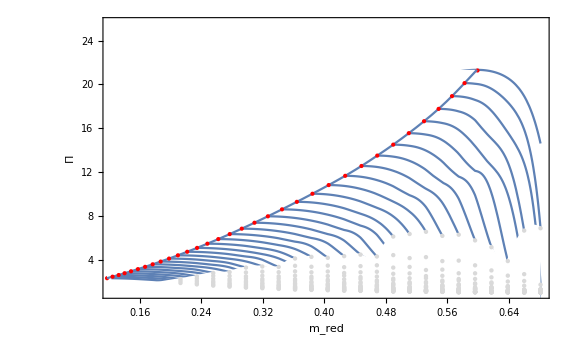

```mathematica
compressorMapFromFile=plotCompressorMapFromFile[32]
```

```mathematica
{AreaRamOnD,mredCompOnD,TratioMaxOnD,NredTurbOnD,PratioTurbOnD,PratioNozzleOnD}=varsOnD
```

{1.21626,0.523737,4.81656,0.0997084,3.17886,1.8506}

```mathematica
{MOnD,nredC,areaComp,diameterComp,p03p02,m3m1,areaTurb,areaNozzle,ηt,ηc,ηn,ηm,γt,γn,γc,Rgas,z}=designPars
```

{0.4,0.218827,0.911419,0.5287,0.95,1.,0.121537,0.335821,0.98,0.87,0.98,0.99,1.33,1.33,1.4,287,1000.}

```mathematica
{systemSolOnD,equipointOnD,NredCompOnD,PratioCompOnD,RPMOnD,mflowOnD,ΔT012OnD,T03OnD,ΔT034OnD,WcompOnD,WturbOnD}=testOffDesignEquiPoint[designPars,varsOnD,True];
```

f_1[x_DES] = 1.11022×10^-16

f_2[x_DES] = 0.0000445456

f_3[x_DES] = 5.55112×10^-17

f_4[x_DES] = 0.000345006

f_5[x_DES] = 0.

f_6[x_DES] = 0.

SelfTest passed

Evaluations→81

{ModulesForAircraftEngine`Private`T03T01→4.81708,ModulesForAircraftEngine`Private`nredT→0.0997031,ModulesForAircraftEngine`Private`mredC→0.523814,ModulesForAircraftEngine`Private`areaIntake→1.21645,ModulesForAircraftEngine`Private`pratioTurb→3.17886,ModulesForAircraftEngine`Private`pratioNozzle→1.8506}

Equilibrium Point              :{0.523814,15.003}

Compressor Reduced MFlow       :0.523814

Compressor Reduced Shaft Speed :0.218827

Compression Ratio              :15.003

RPM                            :119.544

Maximum Temperature Ratio      :4.81708

Turbine Reduced Shaft Speed    :0.0997031

Intake Capture Area            :1.21645

Turbine Expansion Ratio        :3.17886

Nozzle Expansion Ratio         :1.8506

Critical Expansion Ratio       :1.8506

Wcomp [KW]                     :72056.3

Wturb [KW]                     :72056.3

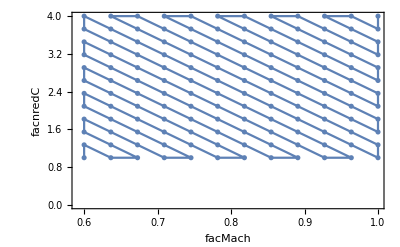

```mathematica
facnredCMin=0.6;facnredCMax=1.0;facMachCMin=1.0;facMachCMax=4.0;
n=12;
listOrderedPoints=MakeOffDesignStates[n,facnredCMin,facnredCMax,facMachCMin,facMachCMax];
nstates=Dimensions[listOrderedPoints][[1]];
distStates=Table[Norm[listOrderedPoints[[i]]-listOrderedPoints[[i-1]]],{i,2,nstates}];
Max[distStates];
ListPlot[Table[{listOrderedPoints[[i,1]],listOrderedPoints[[i,2]]},{i,1,Dimensions[listOrderedPoints][[1]]}],PlotRange->{All,All},Frame->True,FrameLabel->{"facMach","facnredC"},Joined->True,Mesh->All]
```

```mathematica
icount=0;
allDerivedParameters={};
allequipointMredCPRatioC={};
allMachPoints={};
systemSol=systemSolOnD;
For[i=1,i⩽Dimensions[listOrderedPoints][[1]],
icount=icount+1;

facnredC=listOrderedPoints[[i,1]];
facMach=listOrderedPoints[[i,2]];

Print["Equilibrium State  #",icount," {facnredC,facMach} :",listOrderedPoints[[i]]];
offDesignAltitude=10000;
offDesignVars={facMach*MOnD,facnredC*NredCompOnD,offDesignAltitude};
{systemSol,equipoint,NredComp,PratioComp,RPM,mflow,ΔT012,T03,ΔT034,Wcomp,Wturb}=calcOffDesignEquiPoint[designPars,offDesignVars,systemSol,False];
{AreaRam,mredComp,TratioMax,NredTurb,PratioTurb,PratioNozzle}=systemSol;

equipointMredCPRatioC={mredComp/areaComp,PratioComp};
MachPoint={{mredComp/areaComp,PratioComp},facMach*MOnD};

AppendTo[allDerivedParameters,{facMach*MOnD,facnredC*NredCompOnD,AreaRam,mredComp,TratioMax,NredTurb,PratioTurb,PratioNozzle,PratioComp,RPM,mflow,ΔT012,T03,ΔT034,Wcomp,Wturb}];
AppendTo[allequipointMredCPRatioC,equipointMredCPRatioC];
AppendTo[allMachPoints,MachPoint];

Print["Done"];

i++]
```

Equilibrium State  #1 {facnredC,facMach} :{1.,4.}

Evaluations→126

Done

Equilibrium State  #2 {facnredC,facMach} :{1.,3.72727}

Evaluations→106

Done

Equilibrium State  #3 {facnredC,facMach} :{0.963636,4.}

Evaluations→126

Done

Equilibrium State  #4 {facnredC,facMach} :{0.927273,4.}

Evaluations→126

Done

Equilibrium State  #5 {facnredC,facMach} :{0.963636,3.72727}

Evaluations→116

Done

Equilibrium State  #6 {facnredC,facMach} :{1.,3.45455}

Evaluations→116

Done

Equilibrium State  #7 {facnredC,facMach} :{1.,3.18182}

Evaluations→106

Done

Equilibrium State  #8 {facnredC,facMach} :{0.963636,3.45455}

Evaluations→126

Done

Equilibrium State  #9 {facnredC,facMach} :{0.927273,3.72727}

Evaluations→126

Done

Equilibrium State  #10 {facnredC,facMach} :{0.890909,4.}

Evaluations→126

Done

Equilibrium State  #11 {facnredC,facMach} :{0.854545,4.}

Evaluations→121

Done

Equilibrium State  #12 {facnredC,facMach} :{0.890909,3.72727}

Evaluations→116

Done

Equilibrium State  #13 {facnredC,facMach} :{0.927273,3.45455}

Evaluations→116

Done

Equilibrium State  #14 {facnredC,facMach} :{0.963636,3.18182}

Evaluations→116

Done

Equilibrium State  #15 {facnredC,facMach} :{1.,2.90909}

Evaluations→116

Done

Equilibrium State  #16 {facnredC,facMach} :{1.,2.63636}

Evaluations→96

Done

Equilibrium State  #17 {facnredC,facMach} :{0.963636,2.90909}

Evaluations→126

Done

Equilibrium State  #18 {facnredC,facMach} :{0.927273,3.18182}

Evaluations→126

Done

Equilibrium State  #19 {facnredC,facMach} :{0.890909,3.45455}

Evaluations→126

Done

Equilibrium State  #20 {facnredC,facMach} :{0.854545,3.72727}

Evaluations→121

Done

Equilibrium State  #21 {facnredC,facMach} :{0.818182,4.}

Evaluations→121

Done

Equilibrium State  #22 {facnredC,facMach} :{0.781818,4.}

Evaluations→121

Done

Equilibrium State  #23 {facnredC,facMach} :{0.818182,3.72727}

Evaluations→116

Done

Equilibrium State  #24 {facnredC,facMach} :{0.854545,3.45455}

Evaluations→116

Done

Equilibrium State  #25 {facnredC,facMach} :{0.890909,3.18182}

Evaluations→116

Done

Equilibrium State  #26 {facnredC,facMach} :{0.927273,2.90909}

Evaluations→116

Done

Equilibrium State  #27 {facnredC,facMach} :{0.963636,2.63636}

Evaluations→116

Done

Equilibrium State  #28 {facnredC,facMach} :{1.,2.36364}

Evaluations→116

Done

Equilibrium State  #29 {facnredC,facMach} :{1.,2.09091}

Evaluations→106

Done

Equilibrium State  #30 {facnredC,facMach} :{0.963636,2.36364}

Evaluations→126

Done

Equilibrium State  #31 {facnredC,facMach} :{0.927273,2.63636}

Evaluations→126

Done

Equilibrium State  #32 {facnredC,facMach} :{0.890909,2.90909}

Evaluations→126

Done

Equilibrium State  #33 {facnredC,facMach} :{0.854545,3.18182}

Evaluations→121

Done

Equilibrium State  #34 {facnredC,facMach} :{0.818182,3.45455}

Evaluations→121

Done

Equilibrium State  #35 {facnredC,facMach} :{0.781818,3.72727}

Evaluations→121

Done

Equilibrium State  #36 {facnredC,facMach} :{0.745455,4.}

Evaluations→121

Done

Equilibrium State  #37 {facnredC,facMach} :{0.709091,4.}

Evaluations→121

Done

Equilibrium State  #38 {facnredC,facMach} :{0.745455,3.72727}

Evaluations→116

Done

Equilibrium State  #39 {facnredC,facMach} :{0.781818,3.45455}

Evaluations→116

Done

Equilibrium State  #40 {facnredC,facMach} :{0.818182,3.18182}

Evaluations→116

Done

Equilibrium State  #41 {facnredC,facMach} :{0.854545,2.90909}

Evaluations→116

Done

Equilibrium State  #42 {facnredC,facMach} :{0.890909,2.63636}

Evaluations→116

Done

Equilibrium State  #43 {facnredC,facMach} :{0.927273,2.36364}

Evaluations→116

Done

Equilibrium State  #44 {facnredC,facMach} :{0.963636,2.09091}

Evaluations→116

Done

Equilibrium State  #45 {facnredC,facMach} :{1.,1.81818}

Evaluations→116

Done

Equilibrium State  #46 {facnredC,facMach} :{1.,1.54545}

Evaluations→111

Done

Equilibrium State  #47 {facnredC,facMach} :{0.963636,1.81818}

Evaluations→126

Done

Equilibrium State  #48 {facnredC,facMach} :{0.927273,2.09091}

Evaluations→126

Done

Equilibrium State  #49 {facnredC,facMach} :{0.890909,2.36364}

Evaluations→126

Done

Equilibrium State  #50 {facnredC,facMach} :{0.854545,2.63636}

Evaluations→121

Done

Equilibrium State  #51 {facnredC,facMach} :{0.818182,2.90909}

Evaluations→121

Done

Equilibrium State  #52 {facnredC,facMach} :{0.781818,3.18182}

Evaluations→121

Done

Equilibrium State  #53 {facnredC,facMach} :{0.745455,3.45455}

Evaluations→121

Done

Equilibrium State  #54 {facnredC,facMach} :{0.709091,3.72727}

Evaluations→121

Done

Equilibrium State  #55 {facnredC,facMach} :{0.672727,4.}

Evaluations→121

Done

Equilibrium State  #56 {facnredC,facMach} :{0.636364,4.}

Evaluations→121

Done

Equilibrium State  #57 {facnredC,facMach} :{0.672727,3.72727}

Evaluations→116

Done

Equilibrium State  #58 {facnredC,facMach} :{0.709091,3.45455}

Evaluations→116

Done

Equilibrium State  #59 {facnredC,facMach} :{0.745455,3.18182}

Evaluations→116

Done

Equilibrium State  #60 {facnredC,facMach} :{0.781818,2.90909}

Evaluations→116

Done

Equilibrium State  #61 {facnredC,facMach} :{0.818182,2.63636}

Evaluations→116

Done

Equilibrium State  #62 {facnredC,facMach} :{0.854545,2.36364}

Evaluations→116

Done

Equilibrium State  #63 {facnredC,facMach} :{0.890909,2.09091}

Evaluations→116

Done

Equilibrium State  #64 {facnredC,facMach} :{0.927273,1.81818}

Evaluations→116

Done

Equilibrium State  #65 {facnredC,facMach} :{0.963636,1.54545}

Evaluations→116

Done

Equilibrium State  #66 {facnredC,facMach} :{1.,1.27273}

Evaluations→116

Done

Equilibrium State  #67 {facnredC,facMach} :{1.,1.}

Evaluations→121

Done

Equilibrium State  #68 {facnredC,facMach} :{0.963636,1.27273}

Evaluations→126

Done

Equilibrium State  #69 {facnredC,facMach} :{0.927273,1.54545}

Evaluations→126

Done

Equilibrium State  #70 {facnredC,facMach} :{0.890909,1.81818}

Evaluations→126

Done

Equilibrium State  #71 {facnredC,facMach} :{0.854545,2.09091}

Evaluations→121

Done

Equilibrium State  #72 {facnredC,facMach} :{0.818182,2.36364}

Evaluations→121

Done

Equilibrium State  #73 {facnredC,facMach} :{0.781818,2.63636}

Evaluations→121

Done

Equilibrium State  #74 {facnredC,facMach} :{0.745455,2.90909}

Evaluations→121

Done

Equilibrium State  #75 {facnredC,facMach} :{0.709091,3.18182}

Evaluations→121

Done

Equilibrium State  #76 {facnredC,facMach} :{0.672727,3.45455}

Evaluations→121

Done

Equilibrium State  #77 {facnredC,facMach} :{0.636364,3.72727}

Evaluations→121

Done

Equilibrium State  #78 {facnredC,facMach} :{0.6,4.}

Evaluations→121

Done

Equilibrium State  #79 {facnredC,facMach} :{0.6,3.72727}

Evaluations→101

Done

Equilibrium State  #80 {facnredC,facMach} :{0.636364,3.45455}

Evaluations→116

Done

Equilibrium State  #81 {facnredC,facMach} :{0.672727,3.18182}

Evaluations→116

Done

Equilibrium State  #82 {facnredC,facMach} :{0.709091,2.90909}

Evaluations→116

Done

Equilibrium State  #83 {facnredC,facMach} :{0.745455,2.63636}

Evaluations→116

Done

Equilibrium State  #84 {facnredC,facMach} :{0.781818,2.36364}

Evaluations→116

Done

Equilibrium State  #85 {facnredC,facMach} :{0.818182,2.09091}

Evaluations→116

Done

Equilibrium State  #86 {facnredC,facMach} :{0.854545,1.81818}

Evaluations→116

Done

Equilibrium State  #87 {facnredC,facMach} :{0.890909,1.54545}

Evaluations→116

Done

Equilibrium State  #88 {facnredC,facMach} :{0.927273,1.27273}

Evaluations→121

Done

Equilibrium State  #89 {facnredC,facMach} :{0.963636,1.}

Evaluations→121

Done

Equilibrium State  #90 {facnredC,facMach} :{0.927273,1.}

Evaluations→126

Done

Equilibrium State  #91 {facnredC,facMach} :{0.890909,1.27273}

Evaluations→126

Done

Equilibrium State  #92 {facnredC,facMach} :{0.854545,1.54545}

Evaluations→121

Done

Equilibrium State  #93 {facnredC,facMach} :{0.818182,1.81818}

Evaluations→121

Done

Equilibrium State  #94 {facnredC,facMach} :{0.781818,2.09091}

Evaluations→121

Done

Equilibrium State  #95 {facnredC,facMach} :{0.745455,2.36364}

Evaluations→121

Done

Equilibrium State  #96 {facnredC,facMach} :{0.709091,2.63636}

Evaluations→121

Done

Equilibrium State  #97 {facnredC,facMach} :{0.672727,2.90909}

Evaluations→121

Done

Equilibrium State  #98 {facnredC,facMach} :{0.636364,3.18182}

Evaluations→121

Done

Equilibrium State  #99 {facnredC,facMach} :{0.6,3.45455}

Evaluations→121

Done

Equilibrium State  #100 {facnredC,facMach} :{0.6,3.18182}

Evaluations→101

Done

Equilibrium State  #101 {facnredC,facMach} :{0.636364,2.90909}

Evaluations→116

Done

Equilibrium State  #102 {facnredC,facMach} :{0.672727,2.63636}

Evaluations→116

Done

Equilibrium State  #103 {facnredC,facMach} :{0.709091,2.36364}

Evaluations→116

Done

Equilibrium State  #104 {facnredC,facMach} :{0.745455,2.09091}

Evaluations→116

Done

Equilibrium State  #105 {facnredC,facMach} :{0.781818,1.81818}

Evaluations→116

Done

Equilibrium State  #106 {facnredC,facMach} :{0.818182,1.54545}

Evaluations→116

Done

Equilibrium State  #107 {facnredC,facMach} :{0.854545,1.27273}

Evaluations→116

Done

Equilibrium State  #108 {facnredC,facMach} :{0.890909,1.}

Evaluations→121

Done

Equilibrium State  #109 {facnredC,facMach} :{0.854545,1.}

Evaluations→121

Done

Equilibrium State  #110 {facnredC,facMach} :{0.818182,1.27273}

Evaluations→121

Done

Equilibrium State  #111 {facnredC,facMach} :{0.781818,1.54545}

Evaluations→121

Done

Equilibrium State  #112 {facnredC,facMach} :{0.745455,1.81818}

Evaluations→121

Done

Equilibrium State  #113 {facnredC,facMach} :{0.709091,2.09091}

Evaluations→121

Done

Equilibrium State  #114 {facnredC,facMach} :{0.672727,2.36364}

Evaluations→121

Done

Equilibrium State  #115 {facnredC,facMach} :{0.636364,2.63636}

Evaluations→121

Done

Equilibrium State  #116 {facnredC,facMach} :{0.6,2.90909}

Evaluations→121

Done

Equilibrium State  #117 {facnredC,facMach} :{0.6,2.63636}

Evaluations→91

Done

Equilibrium State  #118 {facnredC,facMach} :{0.636364,2.36364}

Evaluations→116

Done

Equilibrium State  #119 {facnredC,facMach} :{0.672727,2.09091}

Evaluations→116

Done

Equilibrium State  #120 {facnredC,facMach} :{0.709091,1.81818}

Evaluations→116

Done

Equilibrium State  #121 {facnredC,facMach} :{0.745455,1.54545}

Evaluations→116

Done

Equilibrium State  #122 {facnredC,facMach} :{0.781818,1.27273}

Evaluations→116

Done

Equilibrium State  #123 {facnredC,facMach} :{0.818182,1.}

Evaluations→121

Done

Equilibrium State  #124 {facnredC,facMach} :{0.781818,1.}

Evaluations→121

Done

Equilibrium State  #125 {facnredC,facMach} :{0.745455,1.27273}

Evaluations→121

Done

Equilibrium State  #126 {facnredC,facMach} :{0.709091,1.54545}

Evaluations→121

Done

Equilibrium State  #127 {facnredC,facMach} :{0.672727,1.81818}

Evaluations→121

Done

Equilibrium State  #128 {facnredC,facMach} :{0.636364,2.09091}

Evaluations→121

Done

Equilibrium State  #129 {facnredC,facMach} :{0.6,2.36364}

Evaluations→121

Done

Equilibrium State  #130 {facnredC,facMach} :{0.6,2.09091}

Evaluations→126

Done

Equilibrium State  #131 {facnredC,facMach} :{0.636364,1.81818}

Evaluations→121

Done

Equilibrium State  #132 {facnredC,facMach} :{0.672727,1.54545}

Evaluations→121

Done

Equilibrium State  #133 {facnredC,facMach} :{0.709091,1.27273}

Evaluations→121

Done

Equilibrium State  #134 {facnredC,facMach} :{0.745455,1.}

Evaluations→121

Done

Equilibrium State  #135 {facnredC,facMach} :{0.709091,1.}

Evaluations→126

Done

Equilibrium State  #136 {facnredC,facMach} :{0.672727,1.27273}

Evaluations→126

Done

Equilibrium State  #137 {facnredC,facMach} :{0.636364,1.54545}

Evaluations→121

Done

Equilibrium State  #138 {facnredC,facMach} :{0.6,1.81818}

Evaluations→121

Done

Equilibrium State  #139 {facnredC,facMach} :{0.6,1.54545}

Evaluations→121

Done

Equilibrium State  #140 {facnredC,facMach} :{0.636364,1.27273}

Evaluations→121

Done

Equilibrium State  #141 {facnredC,facMach} :{0.672727,1.}

Evaluations→121

Done

Equilibrium State  #142 {facnredC,facMach} :{0.636364,1.}

Evaluations→126

Done

Equilibrium State  #143 {facnredC,facMach} :{0.6,1.27273}

Evaluations→121

Done

Equilibrium State  #144 {facnredC,facMach} :{0.6,1.}

Evaluations→121

Done

```mathematica
PaddedForm[TableForm[allDerivedParameters,
TableHeadings->{listOrderedPoints,{"Mach","NredC","AreaRam","mredComp","TratioMax","NredTurb","PratioTurb","PratioNozzle","PRatioC","RPM","massflow","ΔT012","T03","ΔT034","Wcomp","Wturb"}}],{5,4}]
```

| Mach | NredC | AreaRam | mredComp | TratioMax | NredTurb | PratioTurb | PratioNozzle | PRatioC | RPM | massflow | ΔT012 | T03 | ΔT034 | Wcomp | Wturb
{ 1.0000, 4.0000} |  1.6000 |  0.2188 |  0.8696 |  0.5238 |  4.8171 |  0.0997 |  3.1789 |  1.8506 |  15.0030 |  128.8300 |  189.1100 |  453.1600 |  1626.0000 |  397.5100 |  86951.0000 |  86951.0000
{ 1.0000, 3.7273} |  1.4909 |  0.2188 |  0.8346 |  0.5238 |  4.8171 |  0.0997 |  3.1789 |  1.8506 |  15.0030 |  125.9200 |  164.9100 |  432.9500 |  1553.5000 |  379.7800 |  72446.0000 |  72446.0000
{ 0.9636, 4.0000} |  1.6000 |  0.2109 |  0.8002 |  0.4820 |  4.5312 |  0.0991 |  3.1789 |  1.8506 |  13.3900 |  124.1400 |  174.0200 |  426.2700 |  1529.5000 |  373.9200 |  75267.0000 |  75267.0000
{ 0.9273, 4.0000} |  1.6000 |  0.2029 |  0.7282 |  0.4387 |  4.2144 |  0.0988 |  3.1789 |  1.8506 |  11.7520 |  119.4600 |  158.3700 |  396.4700 |  1422.6000 |  347.7800 |  63706.0000 |  63706.0000
{ 0.9636, 3.7273} |  1.4909 |  0.2109 |  0.7680 |  0.4820 |  4.5312 |  0.0991 |  3.1789 |  1.8506 |  13.3900 |  121.3400 |  151.7600 |  407.2600 |  1461.3000 |  357.2500 |  62711.0000 |  62711.0000
{ 1.0000, 3.4545} |  1.3818 |  0.2188 |  0.8060 |  0.5238 |  4.8171 |  0.0997 |  3.1789 |  1.8506 |  15.0030 |  123.1600 |  144.3700 |  414.1700 |  1486.1000 |  363.3000 |  60667.0000 |  60667.0000
{ 1.0000, 3.1818} |  1.2727 |  0.2188 |  0.7844 |  0.5238 |  4.8171 |  0.0997 |  3.1789 |  1.8506 |  15.0030 |  120.5500 |  126.9600 |  396.8100 |  1423.8000 |  348.0800 |  51118.0000 |  51118.0000
{ 0.9636, 3.4545} |  1.3818 |  0.2109 |  0.7417 |  0.4820 |  4.5312 |  0.0991 |  3.1789 |  1.8506 |  13.3900 |  118.6800 |  132.8500 |  389.5900 |  1397.9000 |  341.7500 |  52515.0000 |  52515.0000
{ 0.9273, 3.7273} |  1.4909 |  0.2029 |  0.6989 |  0.4387 |  4.2144 |  0.0988 |  3.1789 |  1.8506 |  11.7520 |  116.7600 |  138.1100 |  378.7900 |  1359.2000 |  332.2700 |  53079.0000 |  53079.0000
{ 0.8909, 4.0000} |  1.6000 |  0.1950 |  0.6584 |  0.3966 |  3.8838 |  0.0989 |  3.1789 |  1.8506 |  10.2010 |  114.7700 |  143.1900 |  365.3700 |  1311.0000 |  320.5000 |  53084.0000 |  53084.0000
{ 0.8545, 4.0000} |  1.6000 |  0.1870 |  0.5938 |  0.3577 |  3.5524 |  0.0992 |  3.1789 |  1.8506 |  8.7977 |  110.0900 |  129.1300 |  334.1900 |  1199.1000 |  293.1500 |  43786.0000 |  43786.0000
{ 0.8909, 3.7273} |  1.4909 |  0.1950 |  0.6319 |  0.3966 |  3.8838 |  0.0989 |  3.1789 |  1.8506 |  10.2010 |  112.1800 |  124.8700 |  349.0700 |  1252.5000 |  306.2100 |  44228.0000 |  44228.0000
{ 0.9273, 3.4545} |  1.3818 |  0.2029 |  0.6750 |  0.4387 |  4.2144 |  0.0988 |  3.1789 |  1.8506 |  11.7520 |  114.2000 |  120.9000 |  362.3500 |  1300.2000 |  317.8500 |  44449.0000 |  44449.0000
{ 0.9636, 3.1818} |  1.2727 |  0.2109 |  0.7218 |  0.4820 |  4.5312 |  0.0991 |  3.1789 |  1.8506 |  13.3900 |  116.1700 |  116.8400 |  373.2600 |  1339.3000 |  327.4200 |  44249.0000 |  44249.0000
{ 1.0000, 2.9091} |  1.1636 |  0.2188 |  0.7705 |  0.5238 |  4.8171 |  0.0997 |  3.1789 |  1.8506 |  15.0030 |  118.1100 |  112.2800 |  380.8800 |  1366.7000 |  334.1000 |  43390.0000 |  43390.0000
{ 1.0000, 2.6364} |  1.0545 |  0.2188 |  0.7649 |  0.5238 |  4.8171 |  0.0997 |  3.1789 |  1.8506 |  15.0030 |  115.8300 |  99.9320 |  366.3700 |  1314.6000 |  321.3800 |  37148.0000 |  37148.0000
{ 0.9636, 2.9091} |  1.1636 |  0.2109 |  0.7090 |  0.4820 |  4.5312 |  0.0991 |  3.1789 |  1.8506 |  13.3900 |  113.8100 |  103.3200 |  358.2800 |  1285.6000 |  314.2800 |  37560.0000 |  37560.0000
{ 0.9273, 3.1818} |  1.2727 |  0.2029 |  0.6569 |  0.4387 |  4.2144 |  0.0988 |  3.1789 |  1.8506 |  11.7520 |  111.7800 |  106.3300 |  347.1600 |  1245.7000 |  304.5300 |  37453.0000 |  37453.0000
{ 0.8909, 3.4545} |  1.3818 |  0.1950 |  0.6103 |  0.3966 |  3.8838 |  0.0989 |  3.1789 |  1.8506 |  10.2010 |  109.7200 |  109.3100 |  333.9300 |  1198.2000 |  292.9200 |  37037.0000 |  37037.0000
{ 0.8545, 3.7273} |  1.4909 |  0.1870 |  0.5699 |  0.3577 |  3.5524 |  0.0992 |  3.1789 |  1.8506 |  8.7977 |  107.6100 |  112.6100 |  319.2800 |  1145.6000 |  280.0700 |  36481.0000 |  36481.0000
{ 0.8182, 4.0000} |  1.6000 |  0.1790 |  0.5358 |  0.3227 |  3.2291 |  0.0996 |  3.1789 |  1.8506 |  7.5680 |  105.4000 |  116.5100 |  303.7800 |  1090.0000 |  266.4700 |  35911.0000 |  35911.0000
{ 0.7818, 4.0000} |  1.6000 |  0.1711 |  0.4845 |  0.2919 |  2.9186 |  0.1001 |  3.1789 |  1.8506 |  6.5073 |  100.7200 |  105.3700 |  274.5700 |  985.2000 |  240.8500 |  29356.0000 |  29356.0000
{ 0.8182, 3.7273} |  1.4909 |  0.1790 |  0.5142 |  0.3227 |  3.2291 |  0.0996 |  3.1789 |  1.8506 |  7.5680 |  103.0300 |  101.6000 |  290.2300 |  1041.4000 |  254.5900 |  29920.0000 |  29920.0000
{ 0.8545, 3.4545} |  1.3818 |  0.1870 |  0.5504 |  0.3577 |  3.5524 |  0.0992 |  3.1789 |  1.8506 |  8.7977 |  105.2400 |  98.5800 |  305.4300 |  1095.9000 |  267.9200 |  30550.0000 |  30550.0000
{ 0.8909, 3.1818} |  1.2727 |  0.1950 |  0.5940 |  0.3966 |  3.8838 |  0.0989 |  3.1789 |  1.8506 |  10.2010 |  107.4000 |  96.1360 |  319.9300 |  1148.0000 |  280.6400 |  31208.0000 |  31208.0000
{ 0.9273, 2.9091} |  1.1636 |  0.2029 |  0.6452 |  0.4387 |  4.2144 |  0.0988 |  3.1789 |  1.8506 |  11.7520 |  109.5200 |  94.0260 |  333.2300 |  1195.7000 |  292.3000 |  31791.0000 |  31791.0000
{ 0.9636, 2.6364} |  1.0545 |  0.2109 |  0.7039 |  0.4820 |  4.5312 |  0.0991 |  3.1789 |  1.8506 |  13.3900 |  111.6200 |  91.9600 |  344.6300 |  1236.6000 |  302.3100 |  32157.0000 |  32157.0000
{ 1.0000, 2.3636} |  0.9455 |  0.2188 |  0.7670 |  0.5238 |  4.8171 |  0.0997 |  3.1789 |  1.8506 |  15.0030 |  113.7500 |  89.6080 |  353.2900 |  1267.7000 |  309.9100 |  32121.0000 |  32121.0000
{ 1.0000, 2.0909} |  0.8364 |  0.2188 |  0.7840 |  0.5238 |  4.8171 |  0.0997 |  3.1789 |  1.8506 |  15.0030 |  111.8600 |  81.0310 |  341.6400 |  1225.9000 |  299.6900 |  28089.0000 |  28089.0000
{ 0.9636, 2.3636} |  0.9455 |  0.2109 |  0.7058 |  0.4820 |  4.5312 |  0.0991 |  3.1789 |  1.8506 |  13.3900 |  109.6100 |  82.4600 |  332.3300 |  1192.5000 |  291.5200 |  27805.0000 |  27805.0000
{ 0.9273, 2.6364} |  1.0545 |  0.2029 |  0.6405 |  0.4387 |  4.2144 |  0.0988 |  3.1789 |  1.8506 |  11.7520 |  107.4100 |  83.6870 |  320.5300 |  1150.1000 |  281.1700 |  27217.0000 |  27217.0000
{ 0.8909, 2.9091} |  1.1636 |  0.1950 |  0.5834 |  0.3966 |  3.8838 |  0.0989 |  3.1789 |  1.8506 |  10.2010 |  105.2200 |  85.0160 |  307.0900 |  1101.9000 |  269.3700 |  26490.0000 |  26490.0000
{ 0.8545, 3.1818} |  1.2727 |  0.1870 |  0.5356 |  0.3577 |  3.5524 |  0.0992 |  3.1789 |  1.8506 |  8.7977 |  103.0200 |  86.6970 |  292.6300 |  1050.0000 |  256.6900 |  25742.0000 |  25742.0000
{ 0.8182, 3.4545} |  1.3818 |  0.1790 |  0.4966 |  0.3227 |  3.2291 |  0.0996 |  3.1789 |  1.8506 |  7.5680 |  100.7700 |  88.9440 |  277.6400 |  996.2100 |  243.5400 |  25056.0000 |  25056.0000
{ 0.7818, 3.7273} |  1.4909 |  0.1711 |  0.4650 |  0.2919 |  2.9186 |  0.1001 |  3.1789 |  1.8506 |  6.5073 |  98.4470 |  91.8930 |  262.3200 |  941.2600 |  230.1100 |  24458.0000 |  24458.0000
{ 0.7455, 4.0000} |  1.6000 |  0.1631 |  0.4399 |  0.2650 |  2.6231 |  0.1007 |  3.1789 |  1.8506 |  5.6006 |  96.0340 |  95.6640 |  246.7600 |  885.4300 |  216.4600 |  23952.0000 |  23952.0000
{ 0.7091, 4.0000} |  1.6000 |  0.1552 |  0.4013 |  0.2418 |  2.3435 |  0.1014 |  3.1789 |  1.8506 |  4.8297 |  91.3500 |  87.2780 |  220.4600 |  791.0700 |  193.3900 |  19523.0000 |  19523.0000
{ 0.7455, 3.7273} |  1.4909 |  0.1631 |  0.4222 |  0.2650 |  2.6231 |  0.1007 |  3.1789 |  1.8506 |  5.6006 |  93.8680 |  83.4260 |  235.7600 |  845.9400 |  206.8000 |  19956.0000 |  19956.0000
{ 0.7818, 3.4545} |  1.3818 |  0.1711 |  0.4491 |  0.2919 |  2.9186 |  0.1001 |  3.1789 |  1.8506 |  6.5073 |  96.2880 |  80.4430 |  250.9400 |  900.4200 |  220.1200 |  20482.0000 |  20482.0000
{ 0.8182, 3.1818} |  1.2727 |  0.1790 |  0.4833 |  0.3227 |  3.2291 |  0.0996 |  3.1789 |  1.8506 |  7.5680 |  98.6320 |  78.2220 |  266.0000 |  954.4600 |  233.3300 |  21112.0000 |  21112.0000
{ 0.8545, 2.9091} |  1.1636 |  0.1870 |  0.5261 |  0.3577 |  3.5524 |  0.0992 |  3.1789 |  1.8506 |  8.7977 |  100.9300 |  76.6680 |  280.8800 |  1007.8000 |  246.3800 |  21850.0000 |  21850.0000
{ 0.8909, 2.6364} |  1.0545 |  0.1950 |  0.5792 |  0.3966 |  3.8838 |  0.0989 |  3.1789 |  1.8506 |  10.2010 |  103.2000 |  75.6680 |  295.3900 |  1059.9000 |  259.1200 |  22679.0000 |  22679.0000
{ 0.9273, 2.3636} |  0.9455 |  0.2029 |  0.6423 |  0.4387 |  4.2144 |  0.0988 |  3.1789 |  1.8506 |  11.7520 |  105.4800 |  75.0410 |  309.0900 |  1109.1000 |  271.1300 |  23534.0000 |  23534.0000
{ 0.9636, 2.0909} |  0.8364 |  0.2109 |  0.7215 |  0.4820 |  4.5312 |  0.0991 |  3.1789 |  1.8506 |  13.3900 |  107.7900 |  74.5670 |  321.3700 |  1153.1000 |  281.9000 |  24315.0000 |  24315.0000
{ 1.0000, 1.8182} |  0.7273 |  0.2188 |  0.8231 |  0.5238 |  4.8171 |  0.0997 |  3.1789 |  1.8506 |  15.0030 |  110.1700 |  73.9710 |  331.4200 |  1189.2000 |  290.7200 |  24874.0000 |  24874.0000
{ 1.0000, 1.5455} |  0.6182 |  0.2188 |  0.8932 |  0.5238 |  4.8171 |  0.0997 |  3.1789 |  1.8506 |  15.0030 |  108.7000 |  68.2350 |  322.6200 |  1157.6000 |  283.0000 |  22336.0000 |  22336.0000
{ 0.9636, 1.8182} |  0.7273 |  0.2109 |  0.7574 |  0.4820 |  4.5312 |  0.0991 |  3.1789 |  1.8506 |  13.3900 |  106.1600 |  68.0700 |  311.7500 |  1118.6000 |  273.4700 |  21532.0000 |  21532.0000
{ 0.9273, 2.0909} |  0.8364 |  0.2029 |  0.6566 |  0.4387 |  4.2144 |  0.0988 |  3.1789 |  1.8506 |  11.7520 |  103.7200 |  67.8590 |  298.9000 |  1072.5000 |  262.1900 |  20580.0000 |  20580.0000
{ 0.8909, 2.3636} |  0.9455 |  0.1950 |  0.5807 |  0.3966 |  3.8838 |  0.0989 |  3.1789 |  1.8506 |  10.2010 |  101.3400 |  67.8500 |  284.8500 |  1022.1000 |  249.8700 |  19610.0000 |  19610.0000
{ 0.8545, 2.6364} |  1.0545 |  0.1870 |  0.5223 |  0.3577 |  3.5524 |  0.0992 |  3.1789 |  1.8506 |  8.7977 |  98.9860 |  68.2380 |  270.1800 |  969.4600 |  237.0000 |  18707.0000 |  18707.0000
{ 0.8182, 2.9091} |  1.1636 |  0.1790 |  0.4747 |  0.3227 |  3.2291 |  0.0996 |  3.1789 |  1.8506 |  7.5680 |  96.6320 |  69.1740 |  255.3200 |  916.1400 |  223.9700 |  17920.0000 |  17920.0000
{ 0.7818, 3.1818} |  1.2727 |  0.1711 |  0.4371 |  0.2919 |  2.9186 |  0.1001 |  3.1789 |  1.8506 |  6.5073 |  94.2480 |  70.7460 |  240.4200 |  862.6800 |  210.9000 |  17258.0000 |  17258.0000
{ 0.7455, 3.4545} |  1.3818 |  0.1631 |  0.4077 |  0.2650 |  2.6231 |  0.1007 |  3.1789 |  1.8506 |  5.6006 |  91.8090 |  73.0310 |  225.5300 |  809.2400 |  197.8300 |  16712.0000 |  16712.0000
{ 0.7091, 3.7273} |  1.4909 |  0.1552 |  0.3852 |  0.2418 |  2.3435 |  0.1014 |  3.1789 |  1.8506 |  4.8297 |  89.2890 |  76.1120 |  210.6300 |  755.7900 |  184.7600 |  16267.0000 |  16267.0000
{ 0.6727, 4.0000} |  1.6000 |  0.1472 |  0.3681 |  0.2218 |  2.0787 |  0.1021 |  3.1789 |  1.8506 |  4.1723 |  86.6650 |  80.0570 |  195.5500 |  701.6900 |  171.5400 |  15885.0000 |  15885.0000
{ 0.6364, 4.0000} |  1.6000 |  0.1393 |  0.3400 |  0.2048 |  1.8297 |  0.1029 |  3.1789 |  1.8506 |  3.6148 |  81.9810 |  73.9300 |  172.1200 |  617.6200 |  150.9900 |  12912.0000 |  12912.0000
{ 0.6727, 3.7273} |  1.4909 |  0.1472 |  0.3533 |  0.2218 |  2.0787 |  0.1021 |  3.1789 |  1.8506 |  4.1723 |  84.7100 |  69.8150 |  186.8300 |  670.3900 |  163.8900 |  13235.0000 |  13235.0000
{ 0.7091, 3.4545} |  1.3818 |  0.1552 |  0.3720 |  0.2418 |  2.3435 |  0.1014 |  3.1789 |  1.8506 |  4.8297 |  87.3310 |  66.6290 |  201.4900 |  722.9900 |  176.7500 |  13622.0000 |  13622.0000
{ 0.7455, 3.1818} |  1.2727 |  0.1631 |  0.3968 |  0.2650 |  2.6231 |  0.1007 |  3.1789 |  1.8506 |  5.6006 |  89.8650 |  64.2280 |  216.0800 |  775.3200 |  189.5400 |  14081.0000 |  14081.0000
{ 0.7818, 2.9091} |  1.1636 |  0.1711 |  0.4293 |  0.2919 |  2.9186 |  0.1001 |  3.1789 |  1.8506 |  6.5073 |  92.3370 |  62.5630 |  230.7700 |  828.0400 |  202.4300 |  14649.0000 |  14649.0000
{ 0.8182, 2.6364} |  1.0545 |  0.1790 |  0.4712 |  0.3227 |  3.2291 |  0.0996 |  3.1789 |  1.8506 |  7.5680 |  94.7740 |  61.5680 |  245.6000 |  881.2500 |  215.4400 |  15342.0000 |  15342.0000
{ 0.8545, 2.3636} |  0.9455 |  0.1870 |  0.5237 |  0.3577 |  3.5524 |  0.0992 |  3.1789 |  1.8506 |  8.7977 |  97.2030 |  61.1880 |  260.5400 |  934.8600 |  228.5400 |  16175.0000 |  16175.0000
{ 0.8909, 2.0909} |  0.8364 |  0.1950 |  0.5936 |  0.3966 |  3.8838 |  0.0989 |  3.1789 |  1.8506 |  10.2010 |  99.6540 |  61.3560 |  275.4500 |  988.3800 |  241.6300 |  17148.0000 |  17148.0000
{ 0.9273, 1.8182} |  0.7273 |  0.2029 |  0.6893 |  0.4387 |  4.2144 |  0.0988 |  3.1789 |  1.8506 |  11.7520 |  102.1600 |  61.9460 |  289.9500 |  1040.4000 |  254.3400 |  18225.0000 |  18225.0000
{ 0.9636, 1.5455} |  0.6182 |  0.2109 |  0.8220 |  0.4820 |  4.5312 |  0.0991 |  3.1789 |  1.8506 |  13.3900 |  104.7500 |  62.7920 |  303.4700 |  1088.9000 |  266.2100 |  19335.0000 |  19335.0000
{ 1.0000, 1.2727} |  0.5091 |  0.2188 |  1.0120 |  0.5238 |  4.8171 |  0.0997 |  3.1789 |  1.8506 |  15.0030 |  107.4500 |  63.6640 |  315.2500 |  1131.2000 |  276.5300 |  20364.0000 |  20364.0000
{ 1.0000, 1.0000} |  0.4000 |  0.2188 |  1.2164 |  0.5238 |  4.8171 |  0.0997 |  3.1789 |  1.8506 |  15.0030 |  106.4300 |  60.1300 |  309.3000 |  1109.8000 |  271.3200 |  18871.0000 |  18871.0000
{ 0.9636, 1.2727} |  0.5091 |  0.2109 |  0.9312 |  0.4820 |  4.5312 |  0.0991 |  3.1789 |  1.8506 |  13.3900 |  103.5400 |  58.5850 |  296.5400 |  1064.0000 |  260.1200 |  17627.0000 |  17627.0000
{ 0.9273, 1.5455} |  0.6182 |  0.2029 |  0.7480 |  0.4387 |  4.2144 |  0.0988 |  3.1789 |  1.8506 |  11.7520 |  100.7900 |  57.1430 |  282.2600 |  1012.8000 |  247.5900 |  16365.0000 |  16365.0000
{ 0.8909, 1.8182} |  0.7273 |  0.1950 |  0.6232 |  0.3966 |  3.8838 |  0.0989 |  3.1789 |  1.8506 |  10.2010 |  98.1520 |  56.0100 |  267.2100 |  958.8000 |  234.3900 |  15186.0000 |  15186.0000
{ 0.8545, 2.0909} |  0.8364 |  0.1870 |  0.5354 |  0.3577 |  3.5524 |  0.0992 |  3.1789 |  1.8506 |  8.7977 |  95.5870 |  55.3320 |  251.9400 |  904.0300 |  221.0000 |  14145.0000 |  14145.0000
{ 0.8182, 2.3636} |  0.9455 |  0.1790 |  0.4725 |  0.3227 |  3.2291 |  0.0996 |  3.1789 |  1.8506 |  7.5680 |  93.0670 |  55.2070 |  236.8300 |  849.7900 |  207.7500 |  13266.0000 |  13266.0000
{ 0.7818, 2.6364} |  1.0545 |  0.1711 |  0.4262 |  0.2919 |  2.9186 |  0.1001 |  3.1789 |  1.8506 |  6.5073 |  90.5620 |  55.6840 |  221.9800 |  796.5100 |  194.7200 |  12542.0000 |  12542.0000
{ 0.7455, 2.9091} |  1.1636 |  0.1631 |  0.3898 |  0.2650 |  2.6231 |  0.1007 |  3.1789 |  1.8506 |  5.6006 |  88.0420 |  56.7980 |  207.4000 |  744.1900 |  181.9300 |  11953.0000 |  11953.0000
{ 0.7091, 3.1818} |  1.2727 |  0.1552 |  0.3620 |  0.2418 |  2.3435 |  0.1014 |  3.1789 |  1.8506 |  4.8297 |  85.4810 |  58.5970 |  193.0500 |  692.6900 |  169.3400 |  11478.0000 |  11478.0000
{ 0.6727, 3.4545} |  1.3818 |  0.1472 |  0.3412 |  0.2218 |  2.0787 |  0.1021 |  3.1789 |  1.8506 |  4.1723 |  82.8520 |  61.1160 |  178.7300 |  641.3000 |  156.7800 |  11083.0000 |  11083.0000
{ 0.6364, 3.7273} |  1.4909 |  0.1393 |  0.3263 |  0.2048 |  1.8297 |  0.1029 |  3.1789 |  1.8506 |  3.6148 |  80.1310 |  64.4730 |  164.4500 |  590.0700 |  144.2500 |  10758.0000 |  10758.0000
{ 0.6000, 4.0000} |  1.6000 |  0.1313 |  0.3163 |  0.1905 |  1.5948 |  0.1040 |  3.1789 |  1.8506 |  3.1398 |  77.2960 |  68.7820 |  150.0300 |  538.3200 |  131.6000 |  10470.0000 |  10470.0000
{ 0.6000, 3.7273} |  1.4909 |  0.1313 |  0.3036 |  0.1905 |  1.5948 |  0.1040 |  3.1789 |  1.8506 |  3.1398 |  75.5530 |  59.9830 |  143.3300 |  514.3100 |  125.7300 |  8723.6000 |  8723.6000
{ 0.6364, 3.4545} |  1.3818 |  0.1393 |  0.3151 |  0.2048 |  1.8297 |  0.1029 |  3.1789 |  1.8506 |  3.6148 |  78.3740 |  56.4390 |  157.3100 |  564.4700 |  137.9900 |  9008.6000 |  9008.6000
{ 0.6727, 3.1818} |  1.2727 |  0.1472 |  0.3321 |  0.2218 |  2.0787 |  0.1021 |  3.1789 |  1.8506 |  4.1723 |  81.0970 |  53.7490 |  171.2400 |  614.4200 |  150.2100 |  9338.6000 |  9338.6000
{ 0.7091, 2.9091} |  1.1636 |  0.1552 |  0.3556 |  0.2418 |  2.3435 |  0.1014 |  3.1789 |  1.8506 |  4.8297 |  83.7480 |  51.8190 |  185.3000 |  664.8800 |  162.5400 |  9742.5000 |  9742.5000
{ 0.7455, 2.6364} |  1.0545 |  0.1631 |  0.3869 |  0.2650 |  2.6231 |  0.1007 |  3.1789 |  1.8506 |  5.6006 |  86.3500 |  50.5530 |  199.5000 |  715.8500 |  175.0000 |  10233.0000 |  10233.0000
{ 0.7818, 2.3636} |  0.9455 |  0.1711 |  0.4274 |  0.2919 |  2.9186 |  0.1001 |  3.1789 |  1.8506 |  6.5073 |  88.9310 |  49.9310 |  214.0600 |  768.0700 |  187.7700 |  10845.0000 |  10845.0000
{ 0.8182, 2.0909} |  0.8364 |  0.1790 |  0.4830 |  0.3227 |  3.2291 |  0.0996 |  3.1789 |  1.8506 |  7.5680 |  91.5190 |  49.9230 |  229.0200 |  821.7700 |  200.8900 |  11601.0000 |  11601.0000
{ 0.8545, 1.8182} |  0.7273 |  0.1870 |  0.5620 |  0.3577 |  3.5524 |  0.0992 |  3.1789 |  1.8506 |  8.7977 |  94.1460 |  50.5110 |  244.4000 |  876.9700 |  214.3900 |  12526.0000 |  12526.0000
{ 0.8909, 1.5455} |  0.6182 |  0.1950 |  0.6763 |  0.3966 |  3.8838 |  0.0989 |  3.1789 |  1.8506 |  10.2010 |  96.8400 |  51.6670 |  260.1200 |  933.3400 |  228.1700 |  13636.0000 |  13636.0000
{ 0.9273, 1.2727} |  0.5091 |  0.2029 |  0.8475 |  0.4387 |  4.2144 |  0.0988 |  3.1789 |  1.8506 |  11.7520 |  99.6350 |  53.3150 |  275.8100 |  989.6500 |  241.9400 |  14920.0000 |  14920.0000
{ 0.9636, 1.0000} |  0.4000 |  0.2109 |  1.1194 |  0.4820 |  4.5312 |  0.0991 |  3.1789 |  1.8506 |  13.3900 |  102.5600 |  55.3330 |  290.9500 |  1044.0000 |  255.2200 |  16335.0000 |  16335.0000
{ 0.9273, 1.0000} |  0.4000 |  0.2029 |  1.0187 |  0.4387 |  4.2144 |  0.0988 |  3.1789 |  1.8506 |  11.7520 |  98.6910 |  50.3550 |  270.6100 |  970.9800 |  237.3700 |  13826.0000 |  13826.0000
{ 0.8909, 1.2727} |  0.5091 |  0.1950 |  0.7662 |  0.3966 |  3.8838 |  0.0989 |  3.1789 |  1.8506 |  10.2010 |  95.7280 |  48.2060 |  254.1700 |  912.0200 |  222.9600 |  12432.0000 |  12432.0000
{ 0.8545, 1.5455} |  0.6182 |  0.1870 |  0.6099 |  0.3577 |  3.5524 |  0.0992 |  3.1789 |  1.8506 |  8.7977 |  92.8880 |  46.5940 |  237.9200 |  853.6900 |  208.7000 |  11248.0000 |  11248.0000
{ 0.8182, 1.8182} |  0.7273 |  0.1790 |  0.5071 |  0.3227 |  3.2291 |  0.0996 |  3.1789 |  1.8506 |  7.5680 |  90.1390 |  45.5730 |  222.1700 |  797.1700 |  194.8800 |  10273.0000 |  10273.0000
{ 0.7818, 2.0909} |  0.8364 |  0.1711 |  0.4369 |  0.2919 |  2.9186 |  0.1001 |  3.1789 |  1.8506 |  6.5073 |  87.4520 |  45.1520 |  207.0000 |  742.7400 |  181.5800 |  9483.2000 |  9483.2000
{ 0.7455, 2.3636} |  0.9455 |  0.1631 |  0.3880 |  0.2650 |  2.6231 |  0.1007 |  3.1789 |  1.8506 |  5.6006 |  84.7940 |  45.3300 |  192.3800 |  690.3000 |  168.7500 |  8848.4000 |  8848.4000
{ 0.7091, 2.6364} |  1.0545 |  0.1552 |  0.3530 |  0.2418 |  2.3435 |  0.1014 |  3.1789 |  1.8506 |  4.8297 |  82.1370 |  46.1210 |  178.2400 |  639.5600 |  156.3500 |  8341.1000 |  8341.1000
{ 0.6727, 2.9091} |  1.1636 |  0.1472 |  0.3262 |  0.2218 |  2.0787 |  0.1021 |  3.1789 |  1.8506 |  4.1723 |  79.4530 |  47.5320 |  164.3600 |  589.7500 |  144.1800 |  7926.8000 |  7926.8000
{ 0.6364, 3.1818} |  1.2727 |  0.1393 |  0.3067 |  0.2048 |  1.8297 |  0.1029 |  3.1789 |  1.8506 |  3.6148 |  76.7140 |  49.6360 |  150.7200 |  540.8100 |  132.2100 |  7590.7000 |  7590.7000
{ 0.6000, 3.4545} |  1.3818 |  0.1313 |  0.2932 |  0.1905 |  1.5948 |  0.1040 |  3.1789 |  1.8506 |  3.1398 |  73.8950 |  52.5090 |  137.1200 |  492.0000 |  120.2800 |  7305.3000 |  7305.3000
{ 0.6000, 3.1818} |  1.2727 |  0.1313 |  0.2853 |  0.1905 |  1.5948 |  0.1040 |  3.1789 |  1.8506 |  3.1398 |  72.3300 |  46.1800 |  131.3700 |  471.3800 |  115.2400 |  6155.4000 |  6155.4000
{ 0.6364, 2.9091} |  1.1636 |  0.1393 |  0.3012 |  0.2048 |  1.8297 |  0.1029 |  3.1789 |  1.8506 |  3.6148 |  75.1580 |  43.8940 |  144.6700 |  519.1000 |  126.9000 |  6443.1000 |  6443.1000
{ 0.6727, 2.6364} |  1.0545 |  0.1472 |  0.3238 |  0.2218 |  2.0787 |  0.1021 |  3.1789 |  1.8506 |  4.1723 |  77.9250 |  42.3060 |  158.1000 |  567.2900 |  138.6800 |  6786.5000 |  6786.5000
{ 0.7091, 2.3636} |  0.9455 |  0.1552 |  0.3540 |  0.2418 |  2.3435 |  0.1014 |  3.1789 |  1.8506 |  4.8297 |  80.6580 |  41.3560 |  171.8800 |  616.7300 |  150.7700 |  7212.3000 |  7212.3000
{ 0.7455, 2.0909} |  0.8364 |  0.1631 |  0.3966 |  0.2650 |  2.6231 |  0.1007 |  3.1789 |  1.8506 |  5.6006 |  83.3840 |  40.9920 |  186.0400 |  667.5300 |  163.1900 |  7737.6000 |  7737.6000
{ 0.7818, 1.8182} |  0.7273 |  0.1711 |  0.4586 |  0.2919 |  2.9186 |  0.1001 |  3.1789 |  1.8506 |  6.5073 |  86.1330 |  41.2180 |  200.8000 |  720.5100 |  176.1400 |  8397.8000 |  8397.8000
{ 0.8182, 1.5455} |  0.6182 |  0.1790 |  0.5503 |  0.3227 |  3.2291 |  0.0996 |  3.1789 |  1.8506 |  7.5680 |  88.9350 |  42.0390 |  216.2700 |  776.0100 |  189.7100 |  9224.9000 |  9224.9000
{ 0.8545, 1.2727} |  0.5091 |  0.1870 |  0.6910 |  0.3577 |  3.5524 |  0.0992 |  3.1789 |  1.8506 |  8.7977 |  91.8200 |  43.4730 |  232.4800 |  834.1800 |  203.9300 |  10255.0000 |  10255.0000
{ 0.8909, 1.0000} |  0.4000 |  0.1950 |  0.9211 |  0.3966 |  3.8838 |  0.0989 |  3.1789 |  1.8506 |  10.2010 |  94.8210 |  45.5300 |  249.3800 |  894.8200 |  218.7500 |  11521.0000 |  11521.0000
{ 0.8545, 1.0000} |  0.4000 |  0.1870 |  0.8306 |  0.3577 |  3.5524 |  0.0992 |  3.1789 |  1.8506 |  8.7977 |  90.9500 |  41.0590 |  228.1000 |  818.4500 |  200.0800 |  9502.7000 |  9502.7000
{ 0.8182, 1.2727} |  0.5091 |  0.1790 |  0.6235 |  0.3227 |  3.2291 |  0.0996 |  3.1789 |  1.8506 |  7.5680 |  87.9130 |  39.2230 |  211.3300 |  758.2800 |  185.3700 |  8410.3000 |  8410.3000
{ 0.7818, 1.5455} |  0.6182 |  0.1711 |  0.4977 |  0.2919 |  2.9186 |  0.1001 |  3.1789 |  1.8506 |  6.5073 |  84.9820 |  38.0220 |  195.4700 |  701.3900 |  171.4700 |  7541.0000 |  7541.0000
{ 0.7455, 1.8182} |  0.7273 |  0.1631 |  0.4164 |  0.2650 |  2.6231 |  0.1007 |  3.1789 |  1.8506 |  5.6006 |  82.1270 |  37.4200 |  180.4700 |  647.5500 |  158.3000 |  6852.0000 |  6852.0000
{ 0.7091, 2.0909} |  0.8364 |  0.1552 |  0.3618 |  0.2418 |  2.3435 |  0.1014 |  3.1789 |  1.8506 |  4.8297 |  79.3170 |  37.3980 |  166.2100 |  596.3900 |  145.8000 |  6306.9000 |  6306.9000
{ 0.6727, 2.3636} |  0.9455 |  0.1472 |  0.3247 |  0.2218 |  2.0787 |  0.1021 |  3.1789 |  1.8506 |  4.1723 |  76.5220 |  37.9350 |  152.4600 |  547.0400 |  133.7300 |  5868.1000 |  5868.1000
{ 0.6364, 2.6364} |  1.0545 |  0.1393 |  0.2990 |  0.2048 |  1.8297 |  0.1029 |  3.1789 |  1.8506 |  3.6148 |  73.7130 |  39.0680 |  139.1600 |  499.3300 |  122.0700 |  5516.3000 |  5516.3000
{ 0.6000, 2.9091} |  1.1636 |  0.1313 |  0.2802 |  0.1905 |  1.5948 |  0.1040 |  3.1789 |  1.8506 |  3.1398 |  70.8630 |  40.8380 |  126.0900 |  452.4500 |  110.6100 |  5224.8000 |  5224.8000
{ 0.6000, 2.6364} |  1.0545 |  0.1313 |  0.2782 |  0.1905 |  1.5948 |  0.1040 |  3.1789 |  1.8506 |  3.1398 |  69.5010 |  36.3470 |  121.2900 |  435.2200 |  106.4000 |  4473.2000 |  4473.2000
{ 0.6364, 2.3636} |  0.9455 |  0.1393 |  0.2998 |  0.2048 |  1.8297 |  0.1029 |  3.1789 |  1.8506 |  3.6148 |  72.3850 |  35.0320 |  134.1900 |  481.5000 |  117.7100 |  4769.8000 |  4769.8000
{ 0.6727, 2.0909} |  0.8364 |  0.1472 |  0.3319 |  0.2218 |  2.0787 |  0.1021 |  3.1789 |  1.8506 |  4.1723 |  75.2490 |  34.3040 |  147.4300 |  529.0000 |  129.3200 |  5131.5000 |  5131.5000
{ 0.7091, 1.8182} |  0.7273 |  0.1552 |  0.3799 |  0.2418 |  2.3435 |  0.1014 |  3.1789 |  1.8506 |  4.8297 |  78.1210 |  34.1400 |  161.2300 |  578.5400 |  141.4300 |  5585.1000 |  5585.1000
{ 0.7455, 1.5455} |  0.6182 |  0.1631 |  0.4519 |  0.2650 |  2.6231 |  0.1007 |  3.1789 |  1.8506 |  5.6006 |  81.0300 |  34.5180 |  175.6800 |  630.3600 |  154.1000 |  6152.9000 |  6152.9000
{ 0.7818, 1.2727} |  0.5091 |  0.1711 |  0.5639 |  0.2919 |  2.9186 |  0.1001 |  3.1789 |  1.8506 |  6.5073 |  84.0060 |  35.4740 |  191.0000 |  685.3600 |  167.5500 |  6875.0000 |  6875.0000
{ 0.8182, 1.0000} |  0.4000 |  0.1790 |  0.7494 |  0.3227 |  3.2291 |  0.0996 |  3.1789 |  1.8506 |  7.5680 |  87.0800 |  37.0460 |  207.3400 |  743.9800 |  181.8800 |  7793.6000 |  7793.6000
{ 0.7818, 1.0000} |  0.4000 |  0.1711 |  0.6778 |  0.2919 |  2.9186 |  0.1001 |  3.1789 |  1.8506 |  6.5073 |  83.2100 |  33.5050 |  187.4000 |  672.4400 |  164.3900 |  6370.9000 |  6370.9000
{ 0.7455, 1.2727} |  0.5091 |  0.1631 |  0.5119 |  0.2650 |  2.6231 |  0.1007 |  3.1789 |  1.8506 |  5.6006 |  80.0990 |  32.2060 |  171.6600 |  615.9600 |  150.5800 |  5609.5000 |  5609.5000
{ 0.7091, 1.5455} |  0.6182 |  0.1552 |  0.4122 |  0.2418 |  2.3435 |  0.1014 |  3.1789 |  1.8506 |  4.8297 |  77.0770 |  31.4920 |  156.9500 |  563.1800 |  137.6800 |  5015.2000 |  5015.2000
{ 0.6727, 1.8182} |  0.7273 |  0.1472 |  0.3483 |  0.2217 |  2.0806 |  0.1021 |  3.1754 |  1.7750 |  4.1728 |  74.1150 |  31.3040 |  143.0300 |  513.6400 |  125.4600 |  4543.0000 |  4543.0000
{ 0.6364, 2.0909} |  0.8364 |  0.1393 |  0.3061 |  0.2045 |  1.8361 |  0.1028 |  3.1657 |  1.7162 |  3.6164 |  71.1820 |  31.6370 |  129.8200 |  467.2600 |  113.8800 |  4167.2000 |  4167.2000
{ 0.6000, 2.3636} |  0.9455 |  0.1313 |  0.2783 |  0.1901 |  1.6044 |  0.1037 |  3.1565 |  1.6817 |  3.1421 |  68.2490 |  32.5180 |  117.0500 |  422.2200 |  102.6800 |  3861.9000 |  3861.9000
{ 0.6000, 2.0909} |  0.8364 |  0.1313 |  0.2822 |  0.1886 |  1.6388 |  0.1026 |  3.0801 |  1.5364 |  3.1501 |  67.1140 |  29.1690 |  113.4800 |  417.0600 |  99.5470 |  3358.7000 |  3358.7000
{ 0.6364, 1.8182} |  0.7273 |  0.1393 |  0.3194 |  0.2033 |  1.8654 |  0.1020 |  3.1075 |  1.5750 |  3.6234 |  70.1080 |  28.7080 |  126.1600 |  460.5100 |  110.6700 |  3674.8000 |  3674.8000
{ 0.6727, 1.5455} |  0.6182 |  0.1472 |  0.3766 |  0.2209 |  2.1004 |  0.1016 |  3.1396 |  1.6357 |  4.1775 |  73.1240 |  28.7730 |  139.3700 |  504.7600 |  122.2500 |  4068.7000 |  4068.7000
{ 0.7091, 1.2727} |  0.5091 |  0.1552 |  0.4666 |  0.2415 |  2.3499 |  0.1012 |  3.1684 |  1.7289 |  4.8312 |  76.1910 |  29.3520 |  153.4100 |  551.8100 |  134.5700 |  4568.7000 |  4568.7000
{ 0.7455, 1.0000} |  0.4000 |  0.1631 |  0.6154 |  0.2650 |  2.6231 |  0.1007 |  3.1789 |  1.8506 |  5.6006 |  79.3400 |  30.4180 |  168.4300 |  604.3400 |  147.7400 |  5198.2000 |  5198.2000
{ 0.7091, 1.0000} |  0.4000 |  0.1552 |  0.5592 |  0.2408 |  2.3681 |  0.1008 |  3.1389 |  1.6341 |  4.8355 |  75.4700 |  27.6400 |  150.6200 |  545.6100 |  132.1200 |  4224.1000 |  4224.1000
{ 0.6727, 1.2727} |  0.5091 |  0.1472 |  0.4242 |  0.2196 |  2.1334 |  0.1008 |  3.0825 |  1.5394 |  4.1851 |  72.2840 |  26.6860 |  136.3900 |  500.9700 |  119.6400 |  3693.1000 |  3693.1000
{ 0.6364, 1.5455} |  0.6182 |  0.1393 |  0.3436 |  0.2015 |  1.9097 |  0.1008 |  3.0247 |  1.4768 |  3.6335 |  69.1720 |  26.2460 |  123.1300 |  458.9400 |  108.0100 |  3278.9000 |  3278.9000
{ 0.6000, 1.8182} |  0.7273 |  0.1313 |  0.2928 |  0.1863 |  1.6904 |  0.1010 |  2.9750 |  1.4354 |  3.1615 |  66.1020 |  26.3140 |  110.5000 |  417.3000 |  96.9260 |  2950.1000 |  2950.1000
{ 0.6000, 1.5455} |  0.6182 |  0.1313 |  0.3134 |  0.1838 |  1.7524 |  0.0992 |  2.8611 |  1.3640 |  3.1746 |  65.2190 |  23.9380 |  108.0200 |  421.1200 |  94.7500 |  2623.6000 |  2623.6000
{ 0.6364, 1.2727} |  0.5091 |  0.1393 |  0.3852 |  0.1994 |  1.9614 |  0.0994 |  2.9355 |  1.4077 |  3.6446 |  68.3770 |  24.2360 |  120.6500 |  460.5900 |  105.8400 |  2967.1000 |  2967.1000
{ 0.6727, 1.0000} |  0.4000 |  0.1472 |  0.5064 |  0.2181 |  2.1711 |  0.0999 |  3.0203 |  1.4727 |  4.1934 |  71.5990 |  25.0340 |  134.0500 |  500.2200 |  117.5900 |  3404.9000 |  3404.9000
{ 0.6364, 1.0000} |  0.4000 |  0.1393 |  0.4584 |  0.1974 |  2.0138 |  0.0981 |  2.8521 |  1.3594 |  3.6551 |  67.7290 |  22.6570 |  118.6900 |  463.9700 |  104.1200 |  2728.6000 |  2728.6000
{ 0.6000, 1.2727} |  0.5091 |  0.1313 |  0.3499 |  0.1811 |  1.8188 |  0.0974 |  2.7522 |  1.3133 |  3.1878 |  64.4700 |  22.0140 |  105.9900 |  427.1100 |  92.9760 |  2367.5000 |  2367.5000
{ 0.6000, 1.0000} |  0.4000 |  0.1313 |  0.4149 |  0.1787 |  1.8836 |  0.0957 |  2.6571 |  1.2774 |  3.1999 |  63.8590 |  20.5090 |  104.3900 |  433.9700 |  91.5730 |  2172.3000 |  2172.3000

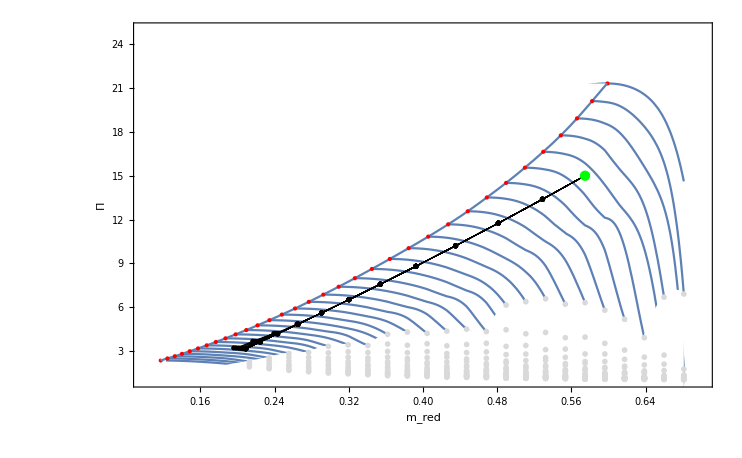

```mathematica
Show[compressorMapFromFile,ListPlot[allequipointMredCPRatioC,PlotStyle->{Thickness[.001],PointSize[Large],Black},Joined->True],
ListPlot[allequipointMredCPRatioC,PlotStyle->{PointSize[.005],Black}],Graphics[{PointSize[0.01],Green,Point[{equipointOnD[[1]]/areaComp,equipointOnD[[2]]}]}],PlotRange->{{0.1,0.7},{1,25}}]
```

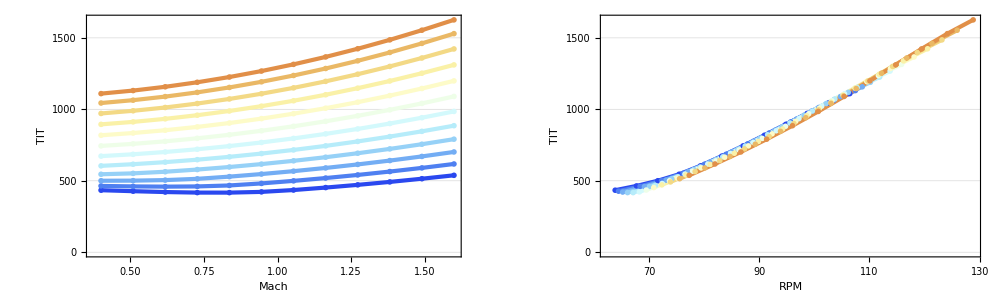

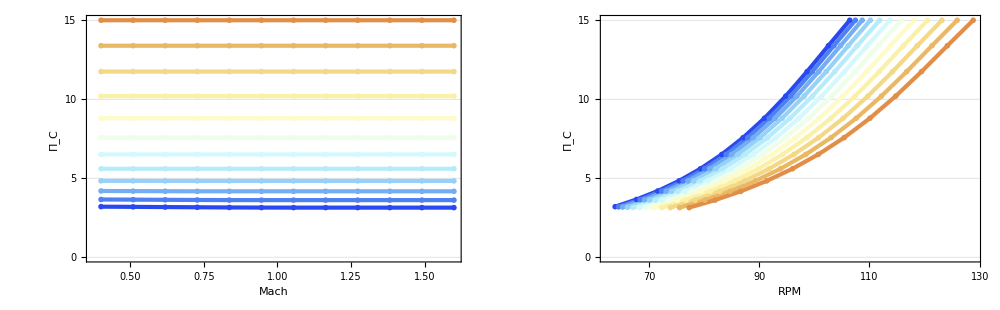

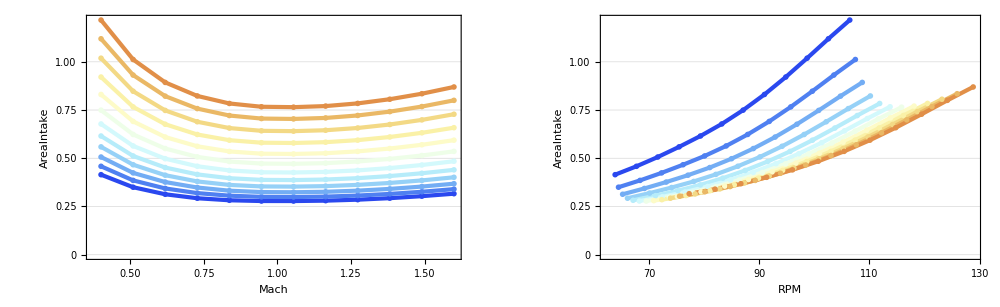

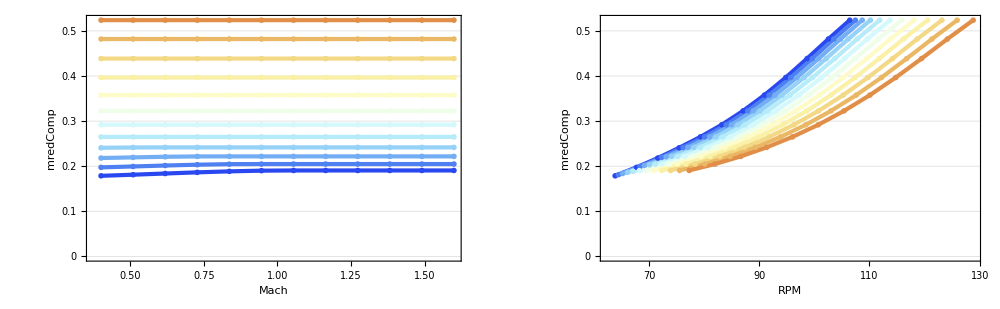

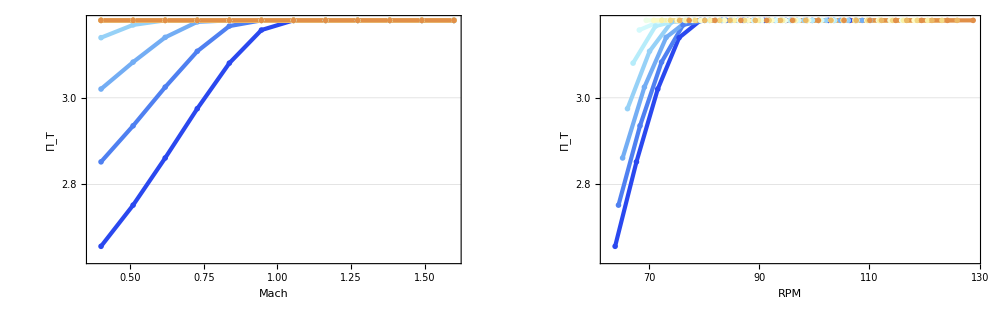

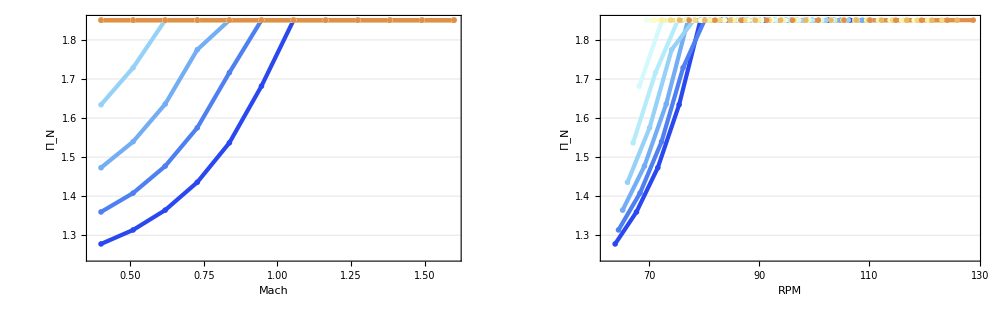

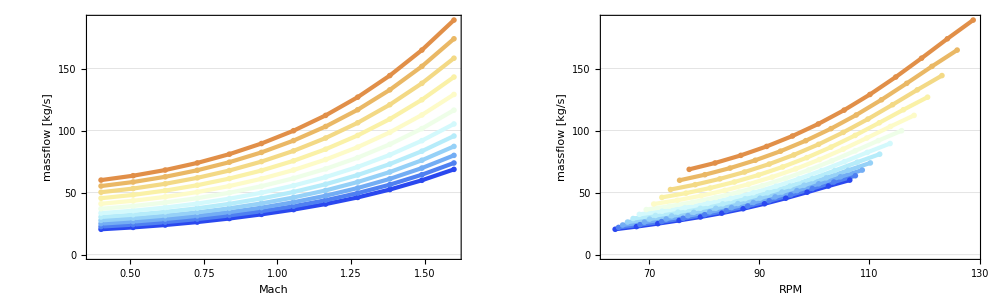

```mathematica
plotOffDesignPerfo[allDerivedParameters,listOrderedPoints,13,"TIT"]
plotOffDesignPerfo[allDerivedParameters,listOrderedPoints,9,"Π_C"]
plotOffDesignPerfo[allDerivedParameters,listOrderedPoints,3,"AreaIntake"]
plotOffDesignPerfo[allDerivedParameters,listOrderedPoints,4,"mredComp"]
plotOffDesignPerfo[allDerivedParameters,listOrderedPoints,7,"Π_T"]
plotOffDesignPerfo[allDerivedParameters,listOrderedPoints,8,"Π_N"]
plotOffDesignPerfo[allDerivedParameters,listOrderedPoints,11,"massflow [kg/s]"]
```

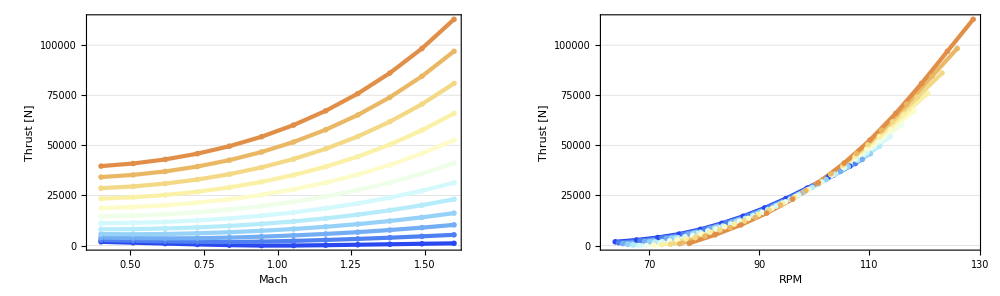
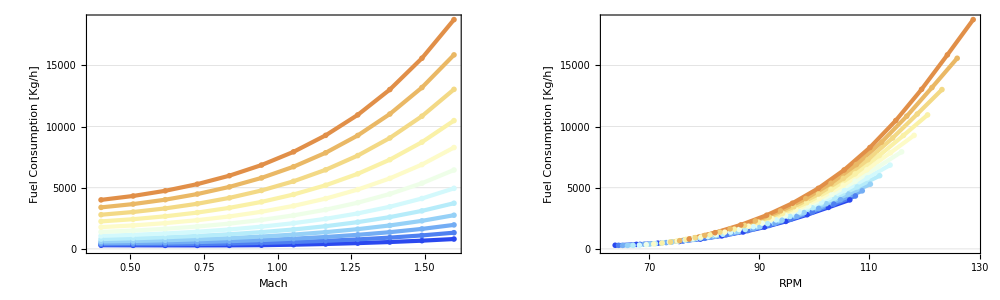
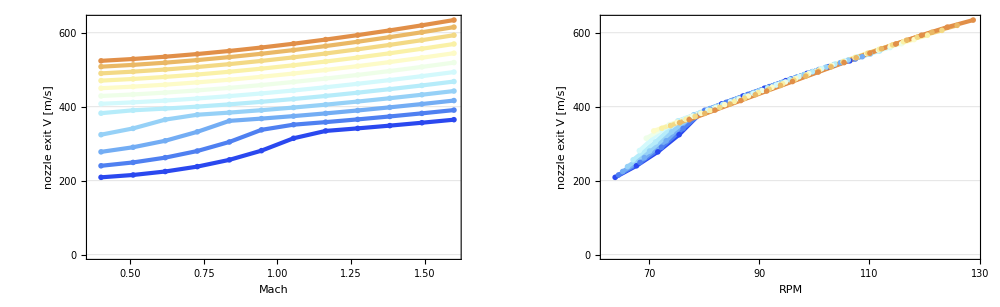
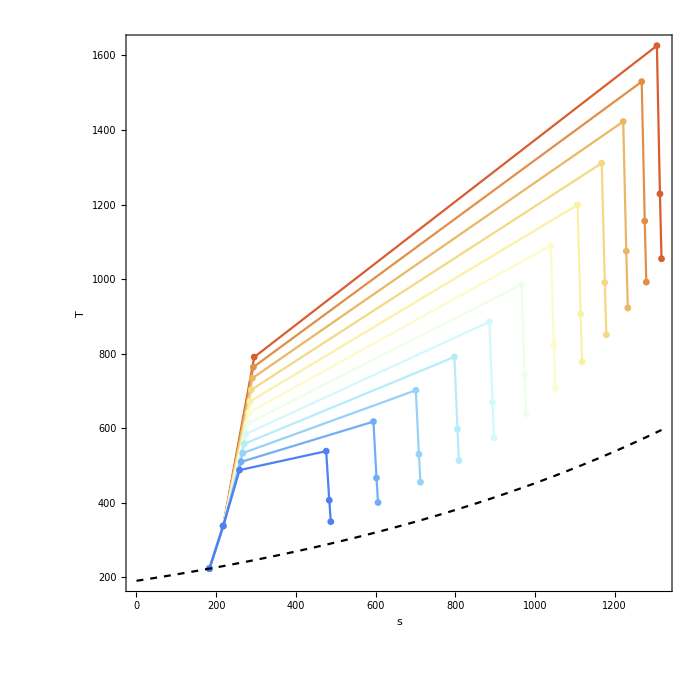
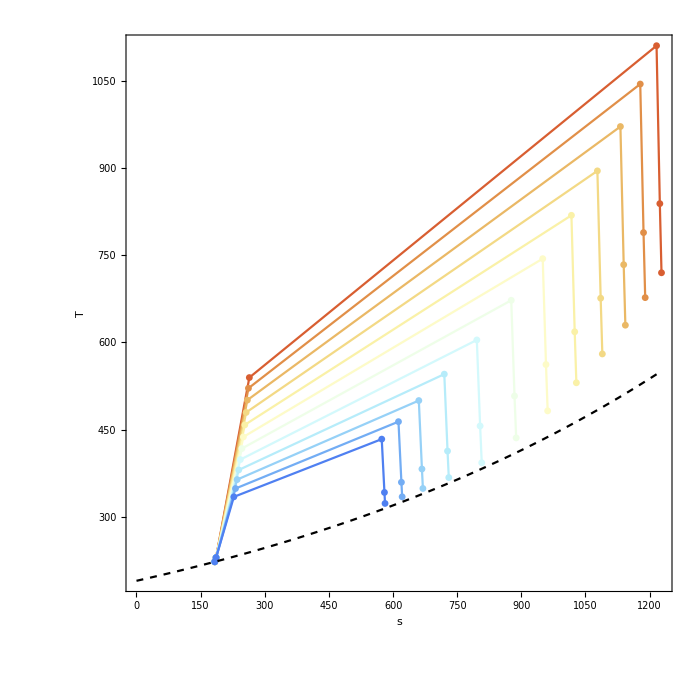

```mathematica
cyclePars={offDesignAltitude,γair,Rair,ηd,ηmc,ηc,Qf,γt,Rgas,ηb,ηpb,ηt,ηmt,ηn};
plotOffDesignCycle[allDerivedParameters,cyclePars,listOrderedPoints]
```

(Cycles are plotted only at the highest and lowest Mach value)